```mathematica
ClearAll["Global`*"]
```

```mathematica
experimentalData = {{5,0.016211939184845394},{8,0.024850762322678507},{10,0.024058805730510315},{15,0.03601337773215673},{20,0.06381716161357727},{25,0.0636923152113714},{30,0.08071719475050237},{40,0.11158931670360221},{70,0.2501894016579193},{80,0.3375066400750176},{100,0.3345147926077956},{200,1.7549184402410392},{300,4.833761436020249},{400,8.500595548223059},{500,9.601506515498142},{600,12.512501226549738}}
```

{{5,0.0162119},{8,0.0248508},{10,0.0240588},{15,0.0360134},{20,0.0638172},{25,0.0636923},{30,0.0807172},{40,0.111589},{70,0.250189},{80,0.337507},{100,0.334515},{200,1.75492},{300,4.83376},{400,8.5006},{500,9.60151},{600,12.5125}}

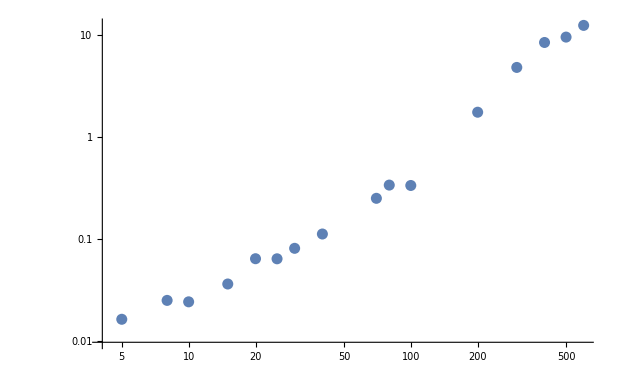

```mathematica
ListLogLogPlot[experimentalData]
```

```mathematica
(*STEP 1:Define giant symbolic model expression*)
(* analyticalBaselineExpression= (0.1 CDL ⅇ^(-t1/(CDL Rsol)) (-1.+ⅇ^(t1/(2 CDL Rsol))))/t1; *)
```

```mathematica
analyticalBaselineExpression= 4 CDL ⅇ^(-2/(CDL fSWV Rsol)) (-1+ⅇ^(1/(4 CDL fSWV Rsol))) (-1+3 ⅇ^(1/(2 CDL fSWV Rsol))-4 ⅇ^(1/(CDL fSWV Rsol))+4 ⅇ^(3/(2 CDL fSWV Rsol))) fSWV V0; (* from analyticalCurrentGivenParams.m *)

analyticalBaselineExpression=analyticalBaselineExpression/.{fSWV->1/(2t1), V0->0.025}
```

(0.05 CDL ⅇ^(-(4 t1)/(CDL Rsol)) (-1+ⅇ^(t1/(2 CDL Rsol))) (-1+3 ⅇ^(t1/(CDL Rsol))-4 ⅇ^((2 t1)/(CDL Rsol))+4 ⅇ^((3 t1)/(CDL Rsol))))/t1

Fitted parameters:

<|Capt→1/1000000,Rct→500,CDL→2.50987×10^-7,Rsol→2202.23|>

<|Capt→1/1000000,Rct→500,CDL→2.50987×10^-7,Rsol→500|>

<|Capt→1/1000000,Rct→500,CDL→2.50987×10^-7,Rsol→1000|>

<|Capt→1/1000000,Rct→500,CDL→2.50987×10^-7,Rsol→2000|>

<|Capt→1/1000000,Rct→500,CDL→2.50987×10^-7,Rsol→2500|>

General::munfl: Exp[-15934.8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7967.42] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3617.89] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

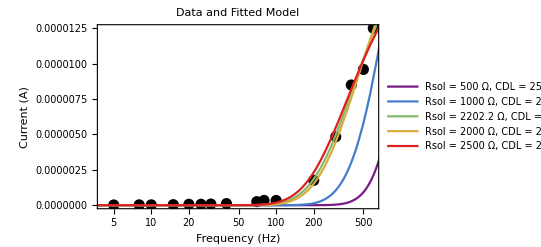

```mathematica
(*STEP 2:Define ModelFunction*)
ModelFunction[frequency_,params_Association]:=Module[{t1Local,expr},
t1Local=1/(2*frequency);
expr=analyticalBaselineExpression/. {CDL->params["CDL"],Rsol->params["Rsol"],Capt->params["Capt"],Rct->params["Rct"],t1->t1Local};
expr
];

(*STEP 3:Define FitFunction*)
FitFunction[data_,constants_Association,initialGuesses_Association,fitVariables_List]:=
Module[{modelFunc,fit,result},(*Define modelFunc as a function of the fit variables*)
modelFunc[f_,cdl_,rsol_]:=ModelFunction[f,Join[constants,<|"CDL"->cdl,"Rsol"->rsol,"Capt"->constants["Capt"],"Rct"->constants["Rct"]|>]];

fit=FindFit[
data,
modelFunc[f,cdl,rsol],
{
{cdl,initialGuesses["CDL"],10^-7,10^-4},
{rsol,initialGuesses["Rsol"],10,10000}
},
f,
Method->{"NMinimize"},
AccuracyGoal->6,
PrecisionGoal->6,
MaxIterations->5000];

result=Join[constants,<|"CDL"->(cdl/. fit),"Rsol"->(rsol/. fit)|>];
result];

(*STEP 4:Example usage*)

data = experimentalData/. {f_,iμA_}:>{f,iμA*10^-6};
(* data=Select[data,#[[1]]>100&]; *)

(*Fixed constants*)
constants=<|"Capt"->1*10^-6,"Rct"->500|>;

(*Initial guesses for fitted variables*)
initialGuesses=<|"CDL"->0.1*10^-6,"Rsol"->1100|>;

fitVariables={"CDL","Rsol"};

result=FitFunction[data,constants,initialGuesses,fitVariables];

Print["Fitted parameters:"];
Print[result];

(*STEP 5:Plot fitted curve vs data*)
result2=ReplacePart[result,"Rsol"->500]
result3=ReplacePart[result,"Rsol"->1000]
result4=ReplacePart[result,"Rsol"->2000]
result5=ReplacePart[result,"Rsol"->2500]

fittedModel[f_]:=ModelFunction[f,result];
fittedModel2[f_]:=ModelFunction[f,result2];
fittedModel3[f_]:=ModelFunction[f,result3];
fittedModel4[f_]:=ModelFunction[f,result4];
fittedModel5[f_]:=ModelFunction[f,result5];

rainbowColors=ColorData["Rainbow"]/@Rescale[Range[5]];

legendLabelBestFit=StringTemplate["Rsol = `` Ω, CDL = `` nF (best fit)"][NumberForm[result["Rsol"],{5,1}],NumberForm[result["CDL"]*10^9,{5,0}]];
legendLabelBestFit2=StringTemplate["Rsol = `` Ω, CDL = `` nF"][NumberForm[result2["Rsol"],{5,1}],NumberForm[result2["CDL"]*10^9,{5,0}]];
legendLabelBestFit3=StringTemplate["Rsol = `` Ω, CDL = `` nF"][NumberForm[result3["Rsol"],{5,1}],NumberForm[result3["CDL"]*10^9,{5,0}]];
legendLabelBestFit4=StringTemplate["Rsol = `` Ω, CDL = `` nF"][NumberForm[result4["Rsol"],{5,1}],NumberForm[result4["CDL"]*10^9,{5,0}]];
legendLabelBestFit5=StringTemplate["Rsol = `` Ω, CDL = `` nF"][NumberForm[result5["Rsol"],{5,1}],NumberForm[result5["CDL"]*10^9,{5,0}]];

(*Put your other labels*)
legendLabels={legendLabelBestFit2, legendLabelBestFit3, legendLabelBestFit, legendLabelBestFit4, legendLabelBestFit5};



Show[ListLogLinearPlot[data,PlotStyle->{Black,PointSize[0.02]},Frame->True,FrameLabel->{"Frequency (Hz)","Current (A)"},PlotLabel->"Data and Fitted Model"],LogLinearPlot[{fittedModel2[f],fittedModel3[f],fittedModel[f],fittedModel4[f],fittedModel5[f]},{f,1,1000},PlotStyle->(Directive[#,Thick]&/@rainbowColors),PlotRange->All,Frame->True,FrameLabel->{"Frequency (Hz)","Current (A)"},PlotLegends->legendLabels,ImageSize->Large]

]
```

(0.05 CDL ⅇ^(-(4 t1)/(CDL Rsol)) (-1+ⅇ^(t1/(2 CDL Rsol))) (-1+3 ⅇ^(t1/(CDL Rsol))-4 ⅇ^((2 t1)/(CDL Rsol))+4 ⅇ^((3 t1)/(CDL Rsol))))/t1

8.24×10^-6 ⅇ^(-2500000/103/Rsol) (-1+ⅇ^(312500/103/Rsol)) (-1+3 ⅇ^(625000/103/Rsol)-4 ⅇ^(1250000/103/Rsol)+4 ⅇ^(1875000/103/Rsol))

General::munfl: Exp[-2407.56] is too small to represent as a normalized machine number; precision may be lost.

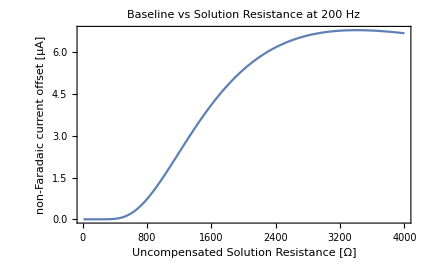

```mathematica
(* ===STEP 6:Current vs Solution Resistance at f=200 Hz===*)

analyticalBaselineExpression
fixedFrequency=200; (*Hz*)
assumedCapacitance = 412*10^-9;
analyticalBaselineExpressionExample = analyticalBaselineExpression/.{t1->1/(2 fixedFrequency), CDL->assumedCapacitance}
Plot[10^6 analyticalBaselineExpressionExample, {Rsol,10,4000}, Frame->True, PlotLabel->"Baseline vs Solution Resistance at 200 Hz",FrameLabel->{"Uncompensated Solution Resistance [Ω]", "non-Faradaic current offset [µA]"}]
```

```mathematica
""
```

<|Capt→1/1000000,Rct→500,CDL→1/10000000,Rsol→2202.23|>

<|Capt→1/1000000,Rct→500,CDL→1/5000000,Rsol→2202.23|>

<|Capt→1/1000000,Rct→500,CDL→1/2500000,Rsol→2202.23|>

<|Capt→1/1000000,Rct→500,CDL→1/2000000,Rsol→2202.23|>

General::munfl: Exp[-9080.43] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4540.22] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3617.89] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

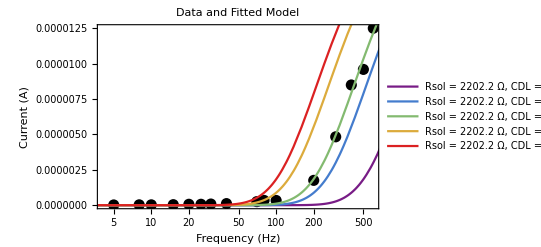

```mathematica
(*STEP 5:Plot fitted curve vs data*)
result2=ReplacePart[result,"CDL"->100*10^-9]
result3=ReplacePart[result,"CDL"->200*10^-9]
result4=ReplacePart[result,"CDL"->400*10^-9]
result5=ReplacePart[result,"CDL"->500*10^-9]

fittedModel[f_]:=ModelFunction[f,result];
fittedModel2[f_]:=ModelFunction[f,result2];
fittedModel3[f_]:=ModelFunction[f,result3]
fittedModel4[f_]:=ModelFunction[f,result4]
fittedModel5[f_]:=ModelFunction[f,result5]

rainbowColors=ColorData["Rainbow"]/@Rescale[Range[5]];

legendLabelBestFit=StringTemplate["Rsol = `` Ω, CDL = `` nF (best fit)"][NumberForm[result["Rsol"],{5,1}],NumberForm[result["CDL"]*10^9,{5,0}]];
legendLabelBestFit2=StringTemplate["Rsol = `` Ω, CDL = `` nF"][NumberForm[result2["Rsol"],{5,1}],NumberForm[result2["CDL"]*10^9,{5,0}]];
legendLabelBestFit3=StringTemplate["Rsol = `` Ω, CDL = `` nF"][NumberForm[result3["Rsol"],{5,1}],NumberForm[result3["CDL"]*10^9,{5,0}]];
legendLabelBestFit4=StringTemplate["Rsol = `` Ω, CDL = `` nF"][NumberForm[result4["Rsol"],{5,1}],NumberForm[result4["CDL"]*10^9,{5,0}]];
legendLabelBestFit5=StringTemplate["Rsol = `` Ω, CDL = `` nF"][NumberForm[result5["Rsol"],{5,1}],NumberForm[result5["CDL"]*10^9,{5,0}]];

(*Put your other labels*)
legendLabels={legendLabelBestFit2, legendLabelBestFit3, legendLabelBestFit, legendLabelBestFit4, legendLabelBestFit5};



Show[ListLogLinearPlot[data,PlotStyle->{Black,PointSize[0.02]},Frame->True,FrameLabel->{"Frequency (Hz)","Current (A)"},PlotLabel->"Data and Fitted Model"],LogLinearPlot[{fittedModel2[f],fittedModel3[f],fittedModel[f],fittedModel4[f],fittedModel5[f]},{f,1,1000},PlotStyle->(Directive[#,Thick]&/@rainbowColors),PlotRange->All,Frame->True,FrameLabel->{"Frequency (Hz)","Current (A)"},PlotLegends->legendLabels,ImageSize->Large]

]
```

General::munfl: Exp[-9080.43] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4540.22] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3617.89] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

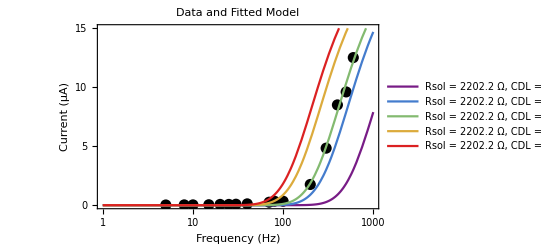

```mathematica
makeOutsideTicksCustom[vals_]:=Table[{x,ToString[x],{0,0.02}},{x,vals}];

makeOutsideLogTicks[min_,max_]:=Module[{major},major=10^Range[Ceiling[Log10[min]],Floor[Log10[max]]];
({#,Superscript[10,Log10[#]],{0,0.02}}&)/@major];

publicationFigureFitRsCDL=Show[ListLogLinearPlot[({#[[1]],10^6*#[[2]]}&)/@data,PlotStyle->{Black,PointSize[0.02]},PlotRange->{{1,1000},{0,15}},Frame->True,Axes->False,FrameLabel->{Style["Frequency (Hz)",16,Bold],Style["Current (µA)",16,Bold]},FrameTicks->{{makeOutsideTicksCustom[{0,5,10,15}],None},{makeOutsideLogTicks[1,1000],None}},FrameTicksStyle->Directive[FontFamily->"Helvetica",FontSize->14,Black],PlotLabel->Style["Data and Fitted Model",18,Bold]],LogLinearPlot[{10^6 fittedModel2[f],10^6 fittedModel3[f],10^6 fittedModel[f],10^6 fittedModel4[f],10^6 fittedModel5[f]},{f,1,1000},PlotStyle->(Directive[#,Thick]&/@rainbowColors),PlotRange->{{1,1000},{-5,15}},Frame->True,Axes->False,FrameLabel->{Style["Frequency (Hz)",16,Bold],Style["Current (µA)",16,Bold]},FrameTicks->{{makeOutsideTicksCustom[{0,5,10,15}],None},{makeOutsideLogTicks[1,1000],None}},FrameTicksStyle->Directive[FontFamily->"Helvetica",FontSize->14,Black],PlotLegends->legendLabels,ImageSize->Large]]
```

```mathematica
Export["publicationFigureFitRsCDL.png",publicationFigureFitRsCDL,ImageResolution->600]

(* DELETE EVERYTHING BEYOND HERE?!?!?! *)


(* analyticalCHICurrentExpression = -((0.1 CDL E^(-(t1/(CDL Rsol))) (-1.+E^(t1/(2 CDL Rsol))))/t1)+(2 (-0.25 2.71828^(-((0.25 (CDL Rsol+Capt (Rct+Rsol)) t1)/(Capt CDL Rct Rsol))) ((Capt CDL^2 (0.2 Rct-0.3 Rsol) Rsol-0.1 CDL^3 Rsol^2+Capt^2 CDL (-0.1 Rct^2-0.3 Rsol^2)+Capt^3 (-0.1 Rct^2-0.2 Rct Rsol-0.1 Rsol^2)) Cosh[(0.25 Sqrt[CDL^2 Rsol^2+2. Capt CDL Rsol (-1. Rct+Rsol)+Capt^2 (Rct+Rsol)^2] t1)/(Capt CDL Rct Rsol)]+(Capt CDL (0.1 Rct-0.2 Rsol)+Capt^2 (-0.1 Rct-0.1 Rsol)-0.1 CDL^2 Rsol) Sqrt[CDL^2 Rsol^2+Capt CDL Rsol (-2. Rct+2. Rsol)+Capt^2 (Rct^2+2. Rct Rsol+Rsol^2)] Sinh[(0.25 Sqrt[CDL^2 Rsol^2+2. Capt CDL Rsol (-1. Rct+Rsol)+Capt^2 (Rct+Rsol)^2] t1)/(Capt CDL Rct Rsol)])+0.25 2.71828^(-((0.5 (CDL Rsol+Capt (Rct+Rsol)) t1)/(Capt CDL Rct Rsol))) ((Capt CDL^2 (0.2 Rct-0.3 Rsol) Rsol-0.1 CDL^3 Rsol^2+Capt^2 CDL (-0.1 Rct^2-0.3 Rsol^2)+Capt^3 (-0.1 Rct^2-0.2 Rct Rsol-0.1 Rsol^2)) Cosh[(0.5 Sqrt[CDL^2 Rsol^2+2. Capt CDL Rsol (-1. Rct+Rsol)+Capt^2 (Rct+Rsol)^2] t1)/(Capt CDL Rct Rsol)]+(Capt CDL (0.1 Rct-0.2 Rsol)+Capt^2 (-0.1 Rct-0.1 Rsol)-0.1 CDL^2 Rsol) Sqrt[CDL^2 Rsol^2+Capt CDL Rsol (-2. Rct+2. Rsol)+Capt^2 (Rct^2+2. Rct Rsol+Rsol^2)] Sinh[(0.5 Sqrt[CDL^2 Rsol^2+2. Capt CDL Rsol (-1. Rct+Rsol)+Capt^2 (Rct+Rsol)^2] t1)/(Capt CDL Rct Rsol)])))/(Sqrt[CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2] Sqrt[CDL^2 Rsol^2+Capt^2 (Rct+Rsol)^2+Capt CDL Rsol (-2. Rct+2. Rsol)] t1)-(2 (-0.25 2.71828^(-((0.25 (CDL Rsol+Capt (Rct+Rsol)) t1)/(Capt CDL Rct Rsol))) ((Capt CDL^2 (-0.2 Rct+0.3 Rsol) Rsol+0.1 CDL^3 Rsol^2+Capt^3 (0.1 Rct^2+0.2 Rct Rsol+0.1 Rsol^2)+Capt^2 CDL (0.1 Rct^2+0.3 Rsol^2)) Cosh[(0.25 Sqrt[CDL^2 Rsol^2+2. Capt CDL Rsol (-1. Rct+Rsol)+Capt^2 (Rct+Rsol)^2] t1)/(Capt CDL Rct Rsol)]+(Capt^2 (0.1 Rct+0.1 Rsol)+Capt CDL (-0.1 Rct+0.2 Rsol)+0.1 CDL^2 Rsol) Sqrt[CDL^2 Rsol^2+Capt CDL Rsol (-2. Rct+2. Rsol)+Capt^2 (Rct^2+2. Rct Rsol+Rsol^2)] Sinh[(0.25 Sqrt[CDL^2 Rsol^2+2. Capt CDL Rsol (-1. Rct+Rsol)+Capt^2 (Rct+Rsol)^2] t1)/(Capt CDL Rct Rsol)])+0.25 2.71828^(-((0.5 (CDL Rsol+Capt (Rct+Rsol)) t1)/(Capt CDL Rct Rsol))) ((Capt CDL^2 (-0.2 Rct+0.3 Rsol) Rsol+0.1 CDL^3 Rsol^2+Capt^3 (0.1 Rct^2+0.2 Rct Rsol+0.1 Rsol^2)+Capt^2 CDL (0.1 Rct^2+0.3 Rsol^2)) Cosh[(0.5 Sqrt[CDL^2 Rsol^2+2. Capt CDL Rsol (-1. Rct+Rsol)+Capt^2 (Rct+Rsol)^2] t1)/(Capt CDL Rct Rsol)]+(Capt^2 (0.1 Rct+0.1 Rsol)+Capt CDL (-0.1 Rct+0.2 Rsol)+0.1 CDL^2 Rsol) Sqrt[CDL^2 Rsol^2+Capt CDL Rsol (-2. Rct+2. Rsol)+Capt^2 (Rct^2+2. Rct Rsol+Rsol^2)] Sinh[(0.5 Sqrt[CDL^2 Rsol^2+2. Capt CDL Rsol (-1. Rct+Rsol)+Capt^2 (Rct+Rsol)^2] t1)/(Capt CDL Rct Rsol)])))/(Sqrt[CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2] Sqrt[CDL^2 Rsol^2+Capt^2 (Rct+Rsol)^2+Capt CDL Rsol (-2. Rct+2. Rsol)] t1) *)


analyticalCHICurrentExpression=1/(√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))0.05 ⅇ^(-(CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(Capt CDL fSWV Rct Rsol)) fSWV (CDL^2 (-1+ⅇ^((2 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(Capt CDL fSWV Rct Rsol))+ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))+3 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol))-3 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol))-4 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol))+4 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol))+4 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(4 Capt CDL fSWV Rct Rsol))-4 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol))+4 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol))-4 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol))-3 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol))+4 ⅇ^((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))-4 ⅇ^((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))+3 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))-ⅇ^((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))) Rsol+Capt CDL (Rct-ⅇ^((2 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(Capt CDL fSWV Rct Rsol)) Rct-ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rct-3 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol)) Rct+3 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol)) Rct+4 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol)) Rct-4 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol)) Rct-4 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(4 Capt CDL fSWV Rct Rsol)) Rct+4 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol)) Rct-4 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol)) Rct+4 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol)) Rct+3 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol)) Rct-4 ⅇ^((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rct+4 ⅇ^((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rct-3 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rct+ⅇ^((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rct-2 Rsol+2 ⅇ^((2 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(Capt CDL fSWV Rct Rsol)) Rsol+2 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rsol+6 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol)) Rsol-6 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol)) Rsol-8 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol)) Rsol+8 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol)) Rsol+8 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(4 Capt CDL fSWV Rct Rsol)) Rsol-8 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol)) Rsol+8 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol)) Rsol-8 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol)) Rsol-6 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol)) Rsol+8 ⅇ^((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rsol-8 ⅇ^((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rsol+6 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rsol-2 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rsol)+Capt^2 (-Rct+ⅇ^((2 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(Capt CDL fSWV Rct Rsol)) Rct+ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rct+3 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol)) Rct-3 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol)) Rct-4 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol)) Rct+4 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol)) Rct+4 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(4 Capt CDL fSWV Rct Rsol)) Rct-4 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol)) Rct+4 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol)) Rct-4 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol)) Rct-3 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol)) Rct+4 ⅇ^((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rct-4 ⅇ^((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rct+3 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rct-ⅇ^((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rct-Rsol+ⅇ^((2 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(Capt CDL fSWV Rct Rsol)) Rsol+ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rsol+3 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol)) Rsol-3 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol)) Rsol-4 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol)) Rsol+4 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol)) Rsol+4 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(4 Capt CDL fSWV Rct Rsol)) Rsol-4 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol)) Rsol+4 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol)) Rsol-4 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol)) Rsol-3 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol)) Rsol+4 ⅇ^((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rsol-4 ⅇ^((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rsol+3 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rsol-ⅇ^((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol)) Rsol)+Capt (1+ⅇ^((2 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(Capt CDL fSWV Rct Rsol))-ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))-3 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol))+3 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol))+4 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol))-4 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol))-4 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(4 Capt CDL fSWV Rct Rsol))+4 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol))+4 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol))-4 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol))-3 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol))+4 ⅇ^((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))-4 ⅇ^((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))+3 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))-ⅇ^((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))) √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)+CDL (1+ⅇ^((2 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(Capt CDL fSWV Rct Rsol))-ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))-3 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol))+3 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol))+4 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol))-4 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol))-4 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(4 Capt CDL fSWV Rct Rsol))+4 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)))/(8 Capt CDL fSWV Rct Rsol))+4 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(2 Capt CDL fSWV Rct Rsol))-4 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol))-3 ⅇ^((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(4 Capt CDL fSWV Rct Rsol))+4 ⅇ^((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))-4 ⅇ^((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))+3 ⅇ^((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))-ⅇ^((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))/(8 Capt CDL fSWV Rct Rsol))) √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2));
analyticalCHICurrentExpression=analyticalCHICurrentExpression/.{fSWV->1/(2t1), V0->0.025}
1/(√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2) t1)0.025 ⅇ^(-(2 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol)) (CDL^2 (-1+ⅇ^((4 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2) t1)/(Capt CDL Rct Rsol))+ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))+3 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol))-3 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))-4 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol))+4 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))+4 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol))-4 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))+4 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol))-4 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol))-3 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol))+4 ⅇ^(((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))-4 ⅇ^(((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))+3 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))-ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))) Rsol+Capt CDL (Rct-ⅇ^((4 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2) t1)/(Capt CDL Rct Rsol)) Rct-ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct-3 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rct+3 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct+4 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol)) Rct-4 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct-4 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rct+4 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct-4 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol)) Rct+4 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rct+3 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rct-4 ⅇ^(((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct+4 ⅇ^(((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct-3 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct+ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct-2 Rsol+2 ⅇ^((4 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2) t1)/(Capt CDL Rct Rsol)) Rsol+2 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol+6 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rsol-6 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol-8 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol)) Rsol+8 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol+8 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rsol-8 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol+8 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol)) Rsol-8 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rsol-6 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rsol+8 ⅇ^(((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol-8 ⅇ^(((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol+6 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol-2 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol)+Capt^2 (-Rct+ⅇ^((4 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2) t1)/(Capt CDL Rct Rsol)) Rct+ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct+3 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rct-3 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct-4 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol)) Rct+4 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct+4 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rct-4 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct+4 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol)) Rct-4 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rct-3 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rct+4 ⅇ^(((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct-4 ⅇ^(((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct+3 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct-ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct-Rsol+ⅇ^((4 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2) t1)/(Capt CDL Rct Rsol)) Rsol+ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol+3 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rsol-3 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol-4 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol)) Rsol+4 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol+4 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rsol-4 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol+4 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol)) Rsol-4 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rsol-3 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rsol+4 ⅇ^(((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol-4 ⅇ^(((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol+3 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol-ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol)+Capt (1+ⅇ^((4 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2) t1)/(Capt CDL Rct Rsol))-ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))-3 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol))+3 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))+4 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol))-4 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))-4 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol))+4 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))+4 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol))-4 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol))-3 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol))+4 ⅇ^(((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))-4 ⅇ^(((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))+3 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))-ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))) √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)+CDL (1+ⅇ^((4 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2) t1)/(Capt CDL Rct Rsol))-ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))-3 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol))+3 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))+4 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol))-4 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))-4 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol))+4 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))+4 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol))-4 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol))-3 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol))+4 ⅇ^(((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))-4 ⅇ^(((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))+3 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))-ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))) √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))
```

publicationFigureFitRsCDL.png

1/(√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2) t1)0.025 ⅇ^(-(2 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol)) (CDL^2 (-1+ⅇ^((4 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2) t1)/(Capt CDL Rct Rsol))+ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))+3 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol))-3 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))-4 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol))+4 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))+4 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol))-4 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))+4 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol))-4 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol))-3 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol))+4 ⅇ^(((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))-4 ⅇ^(((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))+3 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))-ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))) Rsol+Capt CDL (Rct-ⅇ^((4 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2) t1)/(Capt CDL Rct Rsol)) Rct-ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct-3 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rct+3 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct+4 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol)) Rct-4 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct-4 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rct+4 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct-4 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol)) Rct+4 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rct+3 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rct-4 ⅇ^(((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct+4 ⅇ^(((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct-3 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct+ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct-2 Rsol+2 ⅇ^((4 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2) t1)/(Capt CDL Rct Rsol)) Rsol+2 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol+6 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rsol-6 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol-8 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol)) Rsol+8 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol+8 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rsol-8 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol+8 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol)) Rsol-8 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rsol-6 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rsol+8 ⅇ^(((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol-8 ⅇ^(((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol+6 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol-2 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol)+Capt^2 (-Rct+ⅇ^((4 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2) t1)/(Capt CDL Rct Rsol)) Rct+ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct+3 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rct-3 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct-4 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol)) Rct+4 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct+4 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rct-4 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct+4 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol)) Rct-4 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rct-3 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rct+4 ⅇ^(((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct-4 ⅇ^(((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct+3 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct-ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct-Rsol+ⅇ^((4 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2) t1)/(Capt CDL Rct Rsol)) Rsol+ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol+3 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rsol-3 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol-4 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol)) Rsol+4 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol+4 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rsol-4 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol+4 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol)) Rsol-4 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rsol-3 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rsol+4 ⅇ^(((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol-4 ⅇ^(((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol+3 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol-ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol)+Capt (1+ⅇ^((4 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2) t1)/(Capt CDL Rct Rsol))-ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))-3 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol))+3 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))+4 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol))-4 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))-4 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol))+4 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))+4 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol))-4 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol))-3 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol))+4 ⅇ^(((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))-4 ⅇ^(((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))+3 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))-ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))) √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)+CDL (1+ⅇ^((4 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2) t1)/(Capt CDL Rct Rsol))-ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))-3 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol))+3 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))+4 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol))-4 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))-4 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol))+4 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))+4 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol))-4 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol))-3 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol))+4 ⅇ^(((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))-4 ⅇ^(((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))+3 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))-ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))) √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))

1/(√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2) t1)0.025 ⅇ^(-(2 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol)) (CDL^2 (-1+ⅇ^((4 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2) t1)/(Capt CDL Rct Rsol))+ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))+3 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol))-3 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))-4 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol))+4 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))+4 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol))-4 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))+4 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol))-4 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol))-3 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol))+4 ⅇ^(((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))-4 ⅇ^(((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))+3 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))-ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))) Rsol+Capt CDL (Rct-ⅇ^((4 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2) t1)/(Capt CDL Rct Rsol)) Rct-ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct-3 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rct+3 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct+4 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol)) Rct-4 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct-4 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rct+4 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct-4 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol)) Rct+4 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rct+3 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rct-4 ⅇ^(((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct+4 ⅇ^(((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct-3 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct+ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct-2 Rsol+2 ⅇ^((4 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2) t1)/(Capt CDL Rct Rsol)) Rsol+2 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol+6 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rsol-6 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol-8 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol)) Rsol+8 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol+8 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rsol-8 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol+8 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol)) Rsol-8 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rsol-6 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rsol+8 ⅇ^(((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol-8 ⅇ^(((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol+6 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol-2 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol)+Capt^2 (-Rct+ⅇ^((4 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2) t1)/(Capt CDL Rct Rsol)) Rct+ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct+3 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rct-3 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct-4 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol)) Rct+4 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct+4 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rct-4 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct+4 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol)) Rct-4 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rct-3 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rct+4 ⅇ^(((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct-4 ⅇ^(((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct+3 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct-ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rct-Rsol+ⅇ^((4 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2) t1)/(Capt CDL Rct Rsol)) Rsol+ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol+3 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rsol-3 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol-4 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol)) Rsol+4 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol+4 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rsol-4 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol+4 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol)) Rsol-4 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rsol-3 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol)) Rsol+4 ⅇ^(((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol-4 ⅇ^(((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol+3 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol-ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol)) Rsol)+Capt (1+ⅇ^((4 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2) t1)/(Capt CDL Rct Rsol))-ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))-3 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol))+3 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))+4 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol))-4 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))-4 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol))+4 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))+4 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol))-4 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol))-3 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol))+4 ⅇ^(((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))-4 ⅇ^(((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))+3 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))-ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))) √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)+CDL (1+ⅇ^((4 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2) t1)/(Capt CDL Rct Rsol))-ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))-3 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol))+3 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))+4 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol))-4 ⅇ^((5 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))-4 ⅇ^((3 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol))+4 ⅇ^((7 (CDL Rsol+Capt (Rct+Rsol)+√(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))+4 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+3 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(Capt CDL Rct Rsol))-4 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+5 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol))-3 ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+7 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(2 Capt CDL Rct Rsol))+4 ⅇ^(((7 CDL Rsol+7 Capt (Rct+Rsol)+9 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))-4 ⅇ^(((5 CDL Rsol+5 Capt (Rct+Rsol)+11 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))+3 ⅇ^(((3 CDL Rsol+3 Capt (Rct+Rsol)+13 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))-ⅇ^(((CDL Rsol+Capt (Rct+Rsol)+15 √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2)) t1)/(4 Capt CDL Rct Rsol))) √(CDL^2 Rsol^2+2 Capt CDL Rsol (-Rct+Rsol)+Capt^2 (Rct+Rsol)^2))

```mathematica
(* now fit k1 and Gamma from current vs frequency at 0mM, WITH ADDED RESISTOR!! *)
```

```mathematica
zeroConcDataWithResistor ={{5,0.060712215721279675},{8,0.2521637548678694},{10,0.2975490848800591},{15,0.6276718111301997},{20,0.9552192840654037},{25,1.27847803604807},{30,1.56306857263991},{40,2.1228400712086253},{70,3.412127185111575},{80,3.739999663631599},{100,3.919269262064194},{200,5.010193164430636},{300,4.6078791687933105},{400,3.6967780594337185},{500,3.316306154658132},{600,2.611133764328986}}
```

{{5,0.0607122},{8,0.252164},{10,0.297549},{15,0.627672},{20,0.955219},{25,1.27848},{30,1.56307},{40,2.12284},{70,3.41213},{80,3.74},{100,3.91927},{200,5.01019},{300,4.60788},{400,3.69678},{500,3.31631},{600,2.61113}}

```mathematica
(*STEP 2:Define ModelFunction*)
ModelFunction[frequency_,params_Association]:=Module[{t1Local,expr},
t1Local=1/(2*frequency);
expr=analyticalCHICurrentExpression/. {CDL->params["CDL"],Rsol->params["Rsol"],Capt->params["Capt"],Rct->params["Rct"],t1->t1Local};
expr
];

(*STEP 3:Define FitFunction*)
FitFunction[data_,constants_Association,initialGuesses_Association,fitVariables_List]:=
Module[{modelFunc,fit,result},(*Define modelFunc as a function of the fit variables*)
modelFunc[f_,cdl_,rsol_]:=ModelFunction[f,Join[constants,<|"CDL"->constants["CDL"],"Rsol"->constants["Rsol"],"Capt"->capt,"Rct"->rct|>]];

fit=FindFit[
data,
modelFunc[f,capt, rct],
{
{capt,initialGuesses["Capt"],10^-7,10^-4},
{rct,initialGuesses["Rct"],10,100000}
},
f,
Method->{"NMinimize"},
AccuracyGoal->6,
PrecisionGoal->6,
MaxIterations->5000];

result=Join[constants,<|"Capt"->(capt/. fit),"Rct"->(rct/. fit)|>];
result];

(*STEP 4:Example usage*)

data = zeroConcDataWithResistor/. {f_,iμA_}:>{f,iμA*10^-6};
(* data=Select[data,#[[1]]>100&]; *)

(*Fixed constants*)
constants=<|"CDL"->4.1233484307979265*10^-7,"Rsol"->1571.562963748551|>;

(*Initial guesses for fitted variables*)
initialGuesses=<|"Capt"->0.5*10^-6,"Rct"->11000|>;

fitVariables={"Capt","Rct"};

result=FitFunction[data,constants,initialGuesses,fitVariables];

Print["Fitted parameters:"];
Print[result];
```

$Aborted

Fitted parameters:

<|Capt→1/1000000,Rct→500,CDL→2.50987×10^-7,Rsol→2202.23|>

General::munfl: Exp[-771.484] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

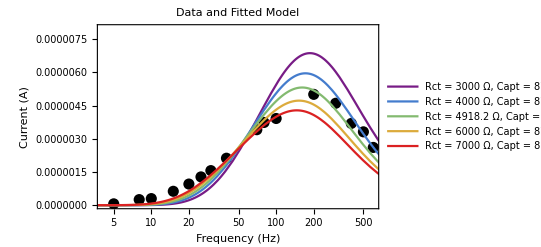

```mathematica
fittedModel[f_]:=ModelFunction[f,result];

result2=ReplacePart[result,"Rct"->3000];
result3=ReplacePart[result,"Rct"->4000];
result4=ReplacePart[result,"Rct"->6000];
result5=ReplacePart[result,"Rct"->7000];
(* 
result4=ReplacePart[result,"Capt"->1*10^-6];
result5=ReplacePart[result,"Capt"->0.4*10^-6];
*)
fittedModel[f_]:=ModelFunction[f,result];
fittedModel2[f_]:=ModelFunction[f,result2];
fittedModel3[f_]:=ModelFunction[f,result3];
fittedModel4[f_]:=ModelFunction[f,result4];
fittedModel5[f_]:=ModelFunction[f,result5];

rainbowColors=ColorData["Rainbow"]/@Rescale[Range[5]];
(*Generate legend label from result*)
legendLabelBestFit=StringTemplate["Rct = `` Ω, Capt = `` nF (best fit)"][NumberForm[result["Rct"],{5,1}],NumberForm[result["Capt"]*10^9,{5,0}]];
legendLabelBestFit2=StringTemplate["Rct = `` Ω, Capt = `` nF"][NumberForm[result2["Rct"],{5,1}],NumberForm[result2["Capt"]*10^9,{5,0}]];
legendLabelBestFit3=StringTemplate["Rct = `` Ω, Capt = `` nF"][NumberForm[result3["Rct"],{5,1}],NumberForm[result3["Capt"]*10^9,{5,0}]];
legendLabelBestFit4=StringTemplate["Rct = `` Ω, Capt = `` nF"][NumberForm[result4["Rct"],{5,1}],NumberForm[result4["Capt"]*10^9,{5,0}]];
legendLabelBestFit5=StringTemplate["Rct = `` Ω, Capt = `` nF"][NumberForm[result5["Rct"],{5,1}],NumberForm[result5["Capt"]*10^9,{5,0}]];

(*Put your other labels*)
legendLabels={legendLabelBestFit2, legendLabelBestFit3, legendLabelBestFit, legendLabelBestFit4, legendLabelBestFit5};

plotRanges = {Automatic, {0,8*10^-6}};
(*Plot*)
Show[ListLogLinearPlot[data,PlotStyle->{Black,PointSize[0.02]},Frame->True,FrameLabel->{"Frequency (Hz)","Current (A)"},PlotLabel->"Data and Fitted Model", PlotRange->plotRanges],LogLinearPlot[{fittedModel2[f],fittedModel3[f],fittedModel[f],fittedModel4[f],fittedModel5[f]},{f,1,1000},PlotStyle->(Directive[#,Thick]&/@rainbowColors), PlotRange->plotRanges,Frame->True,FrameLabel->{"Frequency (Hz)","Current (A)"},PlotLegends->legendLabels,ImageSize->Large]]
```

General::munfl: Exp[-771.484] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

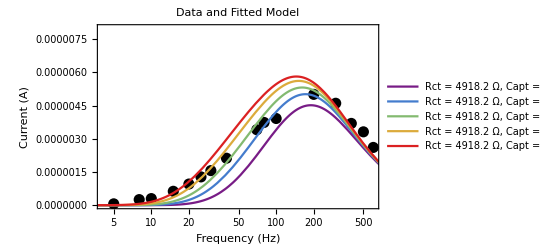

```mathematica
result2=ReplacePart[result,"Capt"->500*10^-9];
result3=ReplacePart[result,"Capt"->700*10^-9];
result4=ReplacePart[result,"Capt"->1100*10^-9];
result5=ReplacePart[result,"Capt"->1300*10^-9];
(* 
result4=ReplacePart[result,"Capt"->1*10^-6];
result5=ReplacePart[result,"Capt"->0.4*10^-6];
*)
fittedModel[f_]:=ModelFunction[f,result];
fittedModel2[f_]:=ModelFunction[f,result2];
fittedModel3[f_]:=ModelFunction[f,result3];
fittedModel4[f_]:=ModelFunction[f,result4];
fittedModel5[f_]:=ModelFunction[f,result5];

rainbowColors=ColorData["Rainbow"]/@Rescale[Range[5]];
(*Generate legend label from result*)
legendLabelBestFit=StringTemplate["Rct = `` Ω, Capt = `` nF (best fit)"][NumberForm[result["Rct"],{5,1}],NumberForm[result["Capt"]*10^9,{5,0}]];
legendLabelBestFit2=StringTemplate["Rct = `` Ω, Capt = `` nF"][NumberForm[result2["Rct"],{5,1}],NumberForm[result2["Capt"]*10^9,{5,0}]];
legendLabelBestFit3=StringTemplate["Rct = `` Ω, Capt = `` nF"][NumberForm[result3["Rct"],{5,1}],NumberForm[result3["Capt"]*10^9,{5,0}]];
legendLabelBestFit4=StringTemplate["Rct = `` Ω, Capt = `` nF"][NumberForm[result4["Rct"],{5,1}],NumberForm[result4["Capt"]*10^9,{5,0}]];
legendLabelBestFit5=StringTemplate["Rct = `` Ω, Capt = `` nF"][NumberForm[result5["Rct"],{5,1}],NumberForm[result5["Capt"]*10^9,{5,0}]];

(*Put your other labels*)
legendLabels={legendLabelBestFit2, legendLabelBestFit3, legendLabelBestFit, legendLabelBestFit4, legendLabelBestFit5};

plotRanges = {Automatic, {0,8*10^-6}};
(*Plot*)
Show[ListLogLinearPlot[data,PlotStyle->{Black,PointSize[0.02]},Frame->True,FrameLabel->{"Frequency (Hz)","Current (A)"},PlotLabel->"Data and Fitted Model", PlotRange->plotRanges],LogLinearPlot[{fittedModel2[f],fittedModel3[f],fittedModel[f],fittedModel4[f],fittedModel5[f]},{f,1,1000},PlotStyle->(Directive[#,Thick]&/@rainbowColors), PlotRange->plotRanges,Frame->True,FrameLabel->{"Frequency (Hz)","Current (A)"},PlotLegends->legendLabels,ImageSize->Large]]
```

```mathematica
(* kD, ...*)
```

```mathematica
deltaIwithResistor =<|0.->{{10,0.2441714793859649358249999999999978742`18.387694934511952},{15,0.50545923539435252582499999999999962185`18.70368613607506},{20,0.76736788888888890524999999999999925121`18.885003621849343},{25,1.02844592425456840549999999999999880497`18.012181461402403},{30,1.24587402409638547799999999999999922396`18.095474131082607},{40,1.68725129950537635599999999999999892086`18.227179771303156},{70,2.63246500123070338449999999999999874831`18.4203626059265},{80,2.86810481293755683924999999999999860696`18.457595018281907},{100,2.99418969799999996275000000000000043301`18.476279311766824},{200,3.68887320000000056699999999999999891976`18.56689372720112},{300,3.31552030000000212600000000000000090186`18.52055169131936},{400,2.62363165783132781549999999999999904868`18.418902862639552},{500,2.34483310353414013475000000000000064491`18.370111936691348},{600,1.83861556705200347724999999999999858493`18.264490932848112}},0.00001->{{10,0.23508480836561099833333333333333230208`18.371224565083434},{15,0.48611033333333329279999999999999920612`18.68673485304728},{20,0.73964334914182472269999999999999848885`18.8690223564371},{25,0.99317903854903495870000000000000135344`18.394967553688122},{30,1.20762185408299867066666666666666538992`18.081930963759618},{40,1.64158329631541239866666666666666617272`18.215262924355848},{70,2.5777214355555556163333333333333344699`18.411235983018273},{80,2.81084947933310290466666666666666717535`18.448837589810466},{100,2.93720530400000019866666666666666720491`18.46793430378467},{200,3.63335530666666782433333333333333527747`18.560307869698548},{300,3.27475445333333480666666666666666799112`18.51517874140863},{400,2.59547407569892533533333333333333361802`18.414216695385115},{500,2.31527014836349622599999999999999868972`18.36460167228639},{600,1.81208160203208527133333333333333203936`18.258177751019755}},0.00004->{{10,0.22747738228438228786666666666666630528`18.35693822192764},{15,0.46760024999999998533333333333333467686`18.669874734683113},{20,0.71287522899729000800000000000000050506`18.853013524101833},{25,0.95929285385452924163333333333333325933`18.981951209253562},{30,1.17174338420348058333333333333333298475`18.06883251012309},{40,1.60273833632307008166666666666666656666`18.204862625057277},{70,2.54782984517006784266666666666666532042`18.406170420613375},{80,2.78694614198730407366666666666666544334`18.445128576010138},{100,2.91591527200000024066666666666666813819`18.464774900497286},{200,3.6288628533333346353333333333333332556`18.55977055509335},{300,3.27416117333333669200000000000000035417`18.51510005411271},{400,2.59594585273954124400000000000000097809`18.414295629537545},{500,2.32279017885436461966666666666666632582`18.366009981095413},{600,1.81632873350339431466666666666666635397`18.259194453340463}},0.0001->{{10,0.21831605383505383356666666666666572701`18.339085672656577},{15,0.44697979166666666603333333333333378391`18.65028788875599},{20,0.68328131669768505696666666666666780686`18.834599545754106},{25,0.92558880671684591726666666666666640626`18.966418093987667},{30,1.13851799866131191800000000000000044052`18.05633990070215},{40,1.57367541244444456666666666666666628858`18.19691515933104},{70,2.54649596740740743399999999999999947119`18.40594299277055},{80,2.79000823271580937566666666666666712592`18.445605484785343},{100,2.92489968533333361366666666666666580251`18.46611097576751},{200,3.66410816000000100699999999999999925226`18.56396828502798},{300,3.31365552000000226533333333333333238427`18.52030735817529},{400,2.63125939791164769200000000000000020537`18.42016366432611},{500,2.35163949493976072033333333333333194573`18.37137074539796},{600,1.84421664675427855833333333333333347838`18.265811937847346}},0.00032->{{10,0.20387898573648572719999999999999871275`18.30937246438036},{15,0.41405447224104189646666666666666797625`18.61705747985882},{20,0.63900372769125290573333333333333318537`18.805503391665475},{25,0.87549582515662654143333333333333346867`18.942254079470565},{30,1.0915581606425701806666666666666668969`18.038046880835992},{40,1.54048012301075270533333333333333399424`18.187656098938294},{70,2.57711760888888871700000000000000015397`18.411134238390243},{80,2.84259235606425695833333333333333178376`18.45371458385317},{100,2.98839174400000003133333333333333522895`18.475437527917737},{200,3.79634261333333400900000000000000048885`18.57936539984736},{300,3.45016664000000196566666666666666635158`18.537840071619566},{400,2.746726453333337564333333333333332584`18.43881541015834},{500,2.46034589333333856733333333333333284385`18.39099616767493},{600,1.93255230158036341200000000000000064138`18.286131256267144}},0.0093->{{10,0.13730575146198831740000000000000021469`18.13768872934083},{15,0.27514920138888887010000000000000126596`18.43956825662418},{20,0.43840038768443242659999999999999946284`18.641870929529997},{25,0.6386974710014801433333333333333331789`18.80529519652079},{30,0.85784933199464521519999999999999834822`18.933411017418347},{40,1.38725186423655913733333333333333200046`18.14215531710639},{70,3.00845235827664390766666666666666741611`18.47834313841322},{80,3.46792382881720416233333333333333230597`18.54006954985156},{100,3.75352986133333366366666666666666529053`18.574439875260538},{200,5.21365922666666701000000000000000089573`18.71714264155905},{300,4.80666133333333572866666666666666750057`18.681843523783332},{400,3.83969194666666779266666666666666545949`18.584296382901545},{500,3.4347724533333370183333333333333345241`18.535897971225257},{600,2.69457687804878548066666666666666543182`18.43049057881572}}|>;
```

```mathematica
deltaIwithNoResistor=<|0.->{{10,0.21269133760387099707500000000000176588`18.327749802514642},{15,0.45779267261195201872500000000000007839`18.66066883711602},{20,0.70208182194264860612500000000000213695`18.846387728579185},{25,0.94337281490333348017500000000000070995`18.97468335706171},{30,1.15560699297188756600000000000000121827`18.062810161244084},{40,1.57414675244526501825000000000000163257`18.197045217734768},{70,2.56136642201761035449999999999999977221`18.408471711883912},{80,2.82302589666454460525000000000000135082`18.4507148621097},{100,2.93641562551803274150000000000000049892`18.467817526412286},{200,4.17846608241521162199999999999999967909`18.62101688124779},{300,4.89312919600000003024999999999999960872`18.689586682829045},{400,5.38180809402987316700000000000000146591`18.730928207513614},{500,5.41214248081194838450000000000000080475`18.73336922137272},{600,5.70525843764873081850000000000000045818`18.756275321936116}},0.00001->{{10,0.20628603213597161356666666666666789258`18.31446982239079},{15,0.44261534827810266313333333333333250189`18.646026469593302},{20,0.68342581692518723693333333333333247007`18.834691380573915},{25,0.91414411422676201346666666666666580125`18.961014667374652},{30,1.12097090093708163133333333333333419251`18.049594338976345},{40,1.52996263973666730366666666666666678751`18.18468082588014},{70,2.50682994810390279233333333333333229984`18.399124874402982},{80,2.76557293405899285499999999999999978432`18.441785116228324},{100,2.87876076307586501033333333333333363534`18.459205574710268},{200,4.10486610017330773566666666666666741533`18.61329899509631},{300,4.81044609765565357933333333333333420161`18.682185352624728},{400,5.29887839778095613500000000000000007443`18.72418395314734},{500,5.34022061066666674400000000000000092761`18.727559198604613},{600,5.61551082837129409533333333333333414359`18.7493892690306}},0.00004->{{10,0.19933517808219177753333333333333484227`18.29958394846879},{15,0.42275353923761424086666666666666792267`18.626087252141883},{20,0.64951725470989647803333333333333133795`18.812590692785115},{25,0.87303555069572216763333333333333475812`18.941031928879244},{30,1.07441790896921009900000000000000046833`18.031173238772425},{40,1.4770313633512544226666666666666668457`18.169389717238673},{70,2.45181909213412094400000000000000088179`18.389488422540353},{80,2.71433454301075256766666666666666783703`18.433663373622032},{100,2.82872579396626510133333333333333179535`18.451590850624523},{200,4.06036286390004455433333333333333460506`18.608564847061817},{300,4.77484030674616081499999999999999905772`18.678958851300145},{400,5.26269224450273225233333333333333279642`18.721207973775172},{500,5.31315919131838962166666666666666664013`18.725352828308647},{600,5.5983078307987707740000000000000011027`18.748056775077206}},0.0001->{{10,0.19150109893814002293333333333333356191`18.282171270531276},{15,0.39919763978746678866666666666666571548`18.601187964904135},{20,0.61134708023018502449999999999999989957`18.786287842373863},{25,0.82360144721877957309999999999999912772`18.915717101081707},{30,1.01945736947791164200000000000000107744`18.0083690696555},{40,1.41786323706294706733333333333333319362`18.151634342092922},{70,2.39609325634844103033333333333333119314`18.37950371685975},{80,2.67198542777124781866666666666666787431`18.4268340852946},{100,2.79110418925718457900000000000000097859`18.445776048589995},{200,4.05449523453199390166666666666666530344`18.607936794304862},{300,4.7785011306666668886666666666666664017`18.679291693105522},{400,5.28019937593556549499999999999999898835`18.722650321441744},{500,5.3362495590566984106666666666666657358`18.72723613192552},{600,5.62335876678289160733333333333333194631`18.74999579211045}},0.00032->{{10,0.17832508004348770653333333333333288843`18.251212427631383},{15,0.36258033052039377226666666666666689199`18.559404240525744},{20,0.5576259752632288905000000000000003521`18.746342995812228},{25,0.75499784597639364313333333333333379567`18.87794571258031},{30,0.94498114376204005463333333333333335674`18.975423142644924},{40,1.34682381083635158633333333333333449536`18.129310785785123},{70,2.38260053345375017366666666666666739741`18.377051234684156},{80,2.6807070537634406199999999999999990646`18.428249357106598},{100,2.81382063423808855933333333333333341792`18.449296410069813},{200,4.19053576964419071333333333333333487345`18.62226955206533},{300,4.98696182167379257333333333333333209257`18.697836043433952},{400,5.53949667939784924699999999999999904167`18.74347030637276},{500,5.60278923215442441266666666666666707967`18.748404285320685},{600,5.93275374777055484633333333333333341628`18.773256322346572}},0.0093->{{10,0.11253202047559327910000000000000070146`18.051276116555655},{15,0.2150699715576820788000000000000018442`18.332579777671643},{20,0.33047940590773504259999999999999932575`18.519144401251925},{25,0.45600899179203487950000000000000063679`18.65897340636435},{30,0.59876538648420846573333333333333165614`18.777256686638623},{40,0.95698181588299165190000000000000008398`18.98090368559638},{70,2.32162205973755634933333333333333418873`18.365791521720457},{80,2.78860175136612036066666666666666770143`18.44538649578853},{100,3.05148764757746778633333333333333409616`18.48451161627203},{200,5.57769872219531669199999999999999868721`18.746455052271056},{300,7.09283383829269839399999999999999920124`18.85081978588013},{400,8.13113975009783916633333333333333397619`18.910151425358542},{500,8.25719108370578341766666666666666715552`18.91683233493366},{600,8.87089361363934463966666666666666804575`18.947967370894247}}|>;
```

```mathematica
ModelFunction[frequency_,concentration_,params_Association]:=
Module[
{theta,RctEff,t1Local,expr},
theta=concentration/(params["kD"]+concentration);
RctEff=1/((1-theta)/params["Rct0"]+theta/params["Rct1"]);
t1Local=1/(2*frequency);
expr=analyticalCHICurrentExpression/. {CDL->params["CDL"],Rsol->params["Rsol"],Capt->params["Capt"],Rct->RctEff,t1->t1Local};
expr
];


(*STEP 3:Define FitFunction*)
FitFunction[allData_List,constants_Association,initialGuesses_Association,fitVariables_List]:=
Module[
{modelFunc,fit,result},
modelFunc[f_,c_,rct0_,rct1_,kD_,capt_]:=ModelFunction[f,c,Join[constants,<|"Rct0"->rct0,"Rct1"->rct1,"kD"->kD,"Capt"->capt|>]];
fit=FindFit[
allData,
modelFunc[f,c,rct0,rct1,kD,capt],
{{rct0,initialGuesses["Rct0"],100,10000},{rct1,initialGuesses["Rct1"],100,10000},{kD,initialGuesses["kD"],1*10^-5,10^-2},{capt,initialGuesses["Capt"],1*10^-8,1*10^-5}},
{f,c},
Method->{"NMinimize"},
AccuracyGoal->6,
PrecisionGoal->6,
MaxIterations->5000];
result=Join[constants,<|"Rct0"->(rct0/. fit),"Rct1"->(rct1/. fit),"kD"->(kD/. fit),"Capt"->(capt/. fit)|>];
result];

(*flatten all data*)


allData=Flatten[KeyValueMap[Function[{conc,curve},curve/. {f_,IμA_}:>{f,conc,IμA*10^-6}],deltaIwithNoResistor],1]; 
constants=<|"CDL"->4.12335*10^-7,"Rsol"->150|>; 

allData=Flatten[KeyValueMap[Function[{conc,curve},curve/. {f_,IμA_}:>{f,conc,IμA*10^-6}],deltaIwithResistor],1];
constants=<|"CDL"->4.12335*10^-7,"Rsol"->1571.56,"Capt"->8.71224*10^-7,"Rct0"->4918.21|>;

allData=Flatten[KeyValueMap[Function[{conc,curve},curve/. {f_,IμA_}:>{f,conc,IμA*10^-6}],deltaIwithResistor],1];
constants=<|"CDL"->4.12335*10^-7,"Rsol"->1571.56|>;


filteredData=allData;

(* 
 filteredData=Select[allData,#[[1]]>=20&]; 
filteredData=Select[filteredData,#[[2]]>=0.0005&] 
filteredData=Select[filteredData,#[[2]]<0.00001&] (* select only zero *)
*)






initialGuesses=<|"Rct0"->5000,"Rct1"->2000,"kD"->2*10^-3,"Capt"->8.7*10^-7|>;

fitVariables={"Rct0","Rct1","kD"};

result=FitFunction[filteredData,constants,initialGuesses,fitVariables];

Print["Fitted parameters:"];
Print[result];
```

Fitted parameters:

<|CDL→4.12335×10^-7,Rsol→1571.56,Rct0→7471.47,Rct1→3259.43,kD→0.00526958,Capt→6.59176×10^-7|>

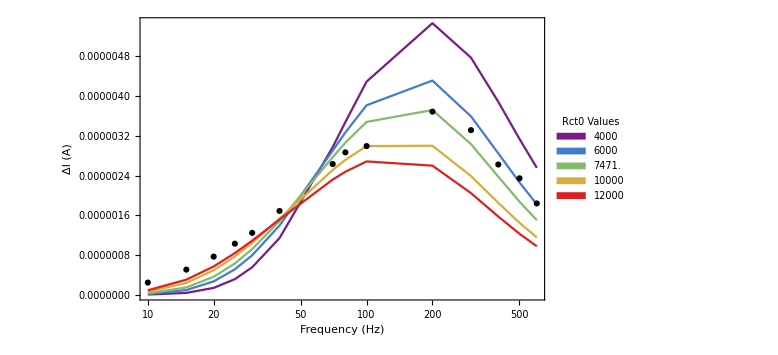

```mathematica
(*Find lowest concentration*)
uniqueConcs=DeleteDuplicates[filteredData[[All,2]]];
minConc=Min[uniqueConcs];

(*Extract data at lowest concentration*)
lowestConcData=Select[filteredData,#[[2]]==minConc&];

(*Extract fitted parameters*)
rct0Fit=result["Rct0"];
rct1Fit=result["Rct1"];
kDFit=result["kD"];
captFit=result["Capt"];

(*Define range of Rct0 values around fit*)
rct0Values={4000,6000,rct0Fit,10000,12000};

(*Define legend labels*)
legendLabels=ToString[NumberForm[#,{6,0}]]&/@rct0Values;

(*Generate rainbow colors*)
colors=ColorData["Rainbow"]/@Rescale[Range[Length[rct0Values]],{1,Length[rct0Values]}];

(*Frequencies to evaluate theory curves*)
frequencies=Sort[lowestConcData[[All,1]]];

(*Generate theory curves as lists of points*)
theoryCurves=Table[Table[{f,ModelFunction[f,minConc,Join[constants,<|"Rct0"->rct0Values[[i]],"Rct1"->rct1Fit,"kD"->kDFit,"Capt"->captFit|>]]},{f,frequencies}],{i,Length[rct0Values]}];

(*Make the theory plot*)
theoryPlot=ListLogLinearPlot[theoryCurves,PlotStyle->(Directive[#,Thick]&/@colors),Joined->True,PlotMarkers->None,Frame->True,FrameLabel->{"Frequency (Hz)","ΔI (A)"},PlotLegends->Placed[SwatchLegend[colors,legendLabels,LegendLabel->"Rct0 Values"],Right],ImageSize->Large];

(*Plot the experimental data*)
expPlot=ListLogLinearPlot[{lowestConcData[[All,{1,3}]]},PlotStyle->{Black},PlotMarkers->{Automatic},Joined->False];

(*Combine plots*)
Show[theoryPlot,expPlot,PlotRange->All]
```

```mathematica
""
```

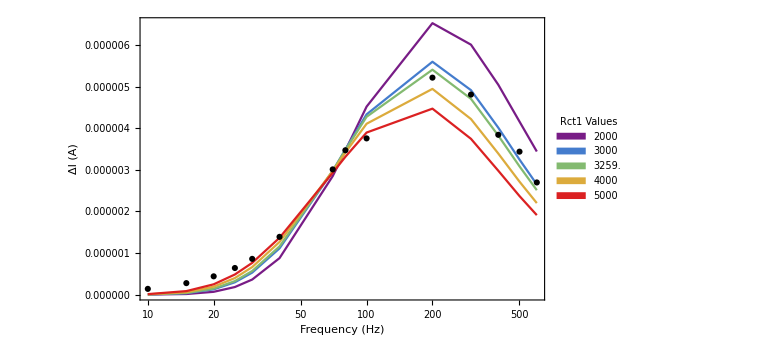

```mathematica
(*Find lowest concentration*)
uniqueConcs=DeleteDuplicates[filteredData[[All,2]]];
maxConc=Max[uniqueConcs];

(*Extract data at lowest concentration*)
highestConcData=Select[filteredData,#[[2]]==maxConc&];

(*Extract fitted parameters*)
rct0Fit=result["Rct0"];
rct1Fit=result["Rct1"];
kDFit=result["kD"];
captFit=result["Capt"];

(*Define range of Rct0 values around fit*)
rct1Values={2000,3000,rct1Fit,4000,5000};

(*Define legend labels*)
legendLabels=ToString[NumberForm[#,{6,0}]]&/@rct1Values;

(*Generate rainbow colors*)
colors=ColorData["Rainbow"]/@Rescale[Range[Length[rct1Values]],{1,Length[rct0Values]}];

(*Frequencies to evaluate theory curves*)
frequencies=Sort[highestConcData[[All,1]]];

(*Generate theory curves as lists of points*)
theoryCurves=Table[Table[{f,ModelFunction[f,maxConc,Join[constants,<|"Rct0"->rct0Fit,"Rct1"->rct1Values[[i]],"kD"->kDFit,"Capt"->captFit|>]]},{f,frequencies}],{i,Length[rct1Values]}];

(*Make the theory plot*)
theoryPlot=ListLogLinearPlot[theoryCurves,PlotStyle->(Directive[#,Thick]&/@colors),Joined->True,PlotMarkers->None,Frame->True,FrameLabel->{"Frequency (Hz)","ΔI (A)"},PlotLegends->Placed[SwatchLegend[colors,legendLabels,LegendLabel->"Rct1 Values"],Right],ImageSize->Large];

(*Plot the experimental data*)
expPlot=ListLogLinearPlot[{highestConcData[[All,{1,3}]]},PlotStyle->{Black},PlotMarkers->{Automatic},Joined->False];

(*Combine plots*)
Show[theoryPlot,expPlot,PlotRange->All]
```

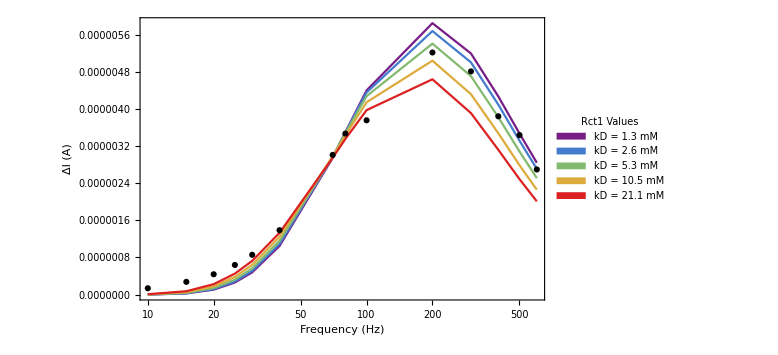

```mathematica
(*Find lowest concentration*)
uniqueConcs=DeleteDuplicates[filteredData[[All,2]]];
maxConc=Max[uniqueConcs];

(*Extract data at lowest concentration*)
highestConcData=Select[filteredData,#[[2]]==maxConc&];

(*Extract fitted parameters*)
rct0Fit=result["Rct0"];
rct1Fit=result["Rct1"];
kDFit=result["kD"];
captFit=result["Capt"];

(*Define range of Rct0 values around fit*)
kDValues={kDFit/4,kDFit/2,kDFit,2*kDFit,4*kDFit};

(*Define legend labels*)
legendLabels=("kD = "<>ToString[NumberForm[1000*#,{6,1}]]<>" mM")&/@kDValues;


(*Generate rainbow colors*)
colors=ColorData["Rainbow"]/@Rescale[Range[Length[kDValues]],{1,Length[kDValues]}];

(*Frequencies to evaluate theory curves*)
frequencies=Sort[highestConcData[[All,1]]];

(*Generate theory curves as lists of points*)
theoryCurves=Table[Table[{f,ModelFunction[f,maxConc,Join[constants,<|"Rct0"->rct0Fit,"Rct1"->rct1Fit,"kD"->kDValues[[i]],"Capt"->captFit|>]]},{f,frequencies}],{i,Length[rct1Values]}];

(*Make the theory plot*)
theoryPlot=ListLogLinearPlot[theoryCurves,PlotStyle->(Directive[#,Thick]&/@colors),Joined->True,PlotMarkers->None,Frame->True,FrameLabel->{"Frequency (Hz)","ΔI (A)"},PlotLegends->Placed[SwatchLegend[colors,legendLabels,LegendLabel->"Rct1 Values"],Right],ImageSize->Large];

(*Plot the experimental data*)
expPlot=ListLogLinearPlot[{highestConcData[[All,{1,3}]]},PlotStyle->{Black},PlotMarkers->{Automatic},Joined->False];

(*Combine plots*)
Show[theoryPlot,expPlot,PlotRange->All]
```

{1.×10^-6,1.25893×10^-6,1.58489×10^-6,1.99526×10^-6,2.51189×10^-6,3.16228×10^-6,3.98107×10^-6,5.01187×10^-6,6.30957×10^-6,7.94328×10^-6,0.00001,0.0000125893,0.0000158489,0.0000199526,0.0000251189,0.0000316228,0.0000398107,0.0000501187,0.0000630957,0.0000794328,0.0001,0.000125893,0.000158489,0.000199526,0.000251189,0.000316228,0.000398107,0.000501187,0.000630957,0.000794328,0.001,0.00125893,0.00158489,0.00199526,0.00251189,0.00316228,0.00398107,0.00501187,0.00630957,0.00794328,0.01,0.0125893,0.0158489,0.0199526,0.0251189,0.0316228,0.0398107,0.0501187,0.0630957,0.0794328,0.1}

<|CDL→4.12335×10^-7,Rsol→1571.56,Rct0→7471.47,Rct1→3259.43,kD→kDval,Capt→6.59176×10^-7|>

{{0.,3.68887320000000057×10^-6},{0.00001,3.63335530666666782×10^-6},{0.00004,3.62886285333333464×10^-6},{0.0001,3.66410816000000101×10^-6},{0.00032,3.79634261333333401×10^-6},{0.0093,5.21365922666666701×10^-6}}

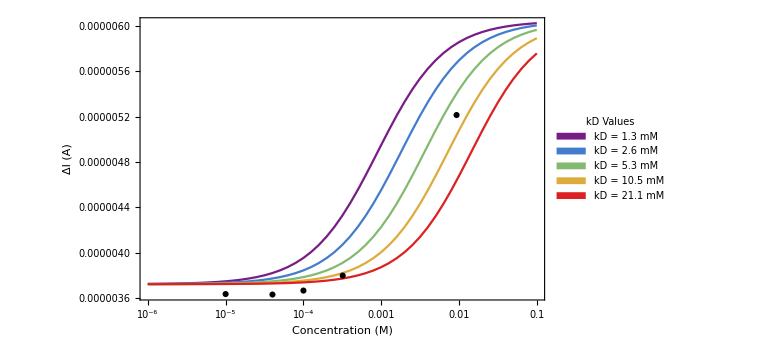

```mathematica
(*-------------------------------------------*)(*Set frequency for plotting ΔI vs conc*)(*-------------------------------------------*)
fPlot=200;  (*e.g.100 Hz*)

(*Define concentration range for x-axis*)
concRange=Table[10^x,{x,Log10[1*10^-6],Log10[1*10^-1],0.1}]

(*Extract fitted parameters*)
rct0Fit=result["Rct0"];
rct1Fit=result["Rct1"];
kDFit=result["kD"];
captFit=result["Capt"];

(*Define range of kD values around fit*)
kDValues={kDFit/4,kDFit/2,kDFit,2*kDFit,4*kDFit};

(*Define legend labels in mM*)
legendLabels=("kD = "<>ToString[NumberForm[1000*#,{6,1}]]<>" mM")&/@kDValues;

(*Generate rainbow colors*)
colors=ColorData["Rainbow"]/@Rescale[Range[Length[kDValues]],{1,Length[kDValues]}];

Join[constants,<|"Rct0"->rct0Fit,"Rct1"->rct1Fit,"kD"->kDval,"Capt"->captFit|>]

(*Generate theory curves:ΔI vs conc for each kD*)
theoryCurves=Table[Table[{conc,ModelFunction[fPlot,conc,Join[constants,<|"Rct0"->rct0Fit,"Rct1"->rct1Fit,"kD"->kDval,"Capt"->captFit|>]]},{conc,concRange}],{kDval,kDValues}];

(*Make the theory plot*)
theoryPlot=ListLogLinearPlot[theoryCurves,PlotStyle->(Directive[#,Thick]&/@colors),Joined->True,PlotMarkers->None,Frame->True,FrameLabel->{"Concentration (M)","ΔI (A)"},PlotLegends->Placed[SwatchLegend[colors,legendLabels,LegendLabel->"kD Values"],Right],ImageSize->Large, PlotRange->{Automatic,{0,Automatic}}];

(*-------------------------------------------------------------*)
(*Plot experimental data as ΔI vs conc at the chosen frequency*)
(*-------------------------------------------------------------*)

(*Extract unique concentrations from data*)
uniqueConcs=DeleteDuplicates[filteredData[[All,2]]];

(*Select only data at chosen frequency*)
expDataAtFreq=Select[filteredData,#[[1]]==fPlot&];

(*Extract {conc,ΔI} pairs*)
expPoints=expDataAtFreq[[All,{2,3}]]

(*Plot experimental data*)
expPlot=ListLogLinearPlot[{expPoints},PlotStyle->{Black},PlotMarkers->{Automatic},Joined->False, PlotRange->{Automatic,{0,Automatic}}];

(*Combine plots*)
Show[theoryPlot,expPlot,PlotRange->{Automatic,{0,Automatic}}]
```

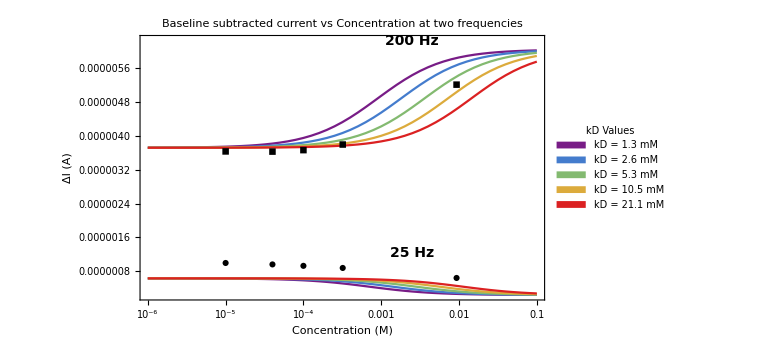

```mathematica
(*Define the frequencies you want plotted*)fPlot={25,200};

(*Define concentration range*)
concRange=Table[10^x,{x,Log10[1*10^-6],Log10[1*10^-1],0.1}];

(*Extract fitted parameters*)
rct0Fit=result["Rct0"];
rct1Fit=result["Rct1"];
kDFit=result["kD"];
captFit=result["Capt"];

(*Define range of kD values around the fit*)
kDValues={kDFit/4,kDFit/2,kDFit,2*kDFit,4*kDFit};

(*Generate legend labels in mM*)
legendLabels=("kD = "<>ToString[NumberForm[1000*#,{6,1}]]<>" mM")&/@kDValues;

(*Generate rainbow colors for the different kD curves*)
colors=ColorData["Rainbow"]/@Rescale[Range[Length[kDValues]],{1,Length[kDValues]}];

(*------------------------------------------------------------*)
(*Compute theory curves for all frequencies and kD values*)
(*------------------------------------------------------------*)

(*Will store curves for each freq and kD value*)
theoryCurvesAll=Flatten[Table[Table[Table[{conc,ModelFunction[f,conc,Join[constants,<|"Rct0"->rct0Fit,"Rct1"->rct1Fit,"kD"->kDval,"Capt"->captFit|>]]},{conc,concRange}],{kDval,kDValues}],{f,fPlot}],1];

(*We’ll build plot styles to distinguish frequencies and kD*)

(*There are Length(kDValues) curves per frequency*)
freqStyles={Solid,Solid};  (*e.g.one style per frequency*)

plotStyles=Flatten[Table[Directive[colors[[k]],freqStyles[[fIndex]],Thick],{fIndex,Length[fPlot]},{k,Length[kDValues]}],1];

(*------------------------------------------------------------*)
(*Experimental data for both frequencies*)
(*------------------------------------------------------------*)

(*Separate experimental points by frequency*)
expDataByFreq=Table[Select[filteredData,#[[1]]==f&][[All,{2,3}]],{f,fPlot}];

(*Compute label positions*)
labelPrimitives=Table[Module[{data,meanX,maxY,labelPos},data=expDataByFreq[[i]];
If[Length[data]>0,meanX=Mean[data[[All,1]]];
maxY=Max[data[[All,2]]];
labelPos={meanX-6,maxY*1.2};(*place label 10% above max*)Text[Style[ToString[fPlot[[i]]]<>" Hz",Black,Bold,14],labelPos],Nothing]],{i,Length[fPlot]}];

(*------------------------------------------------------------*)
(*Plot everything together*)
(*------------------------------------------------------------*)

combinedPlot=Show[ListLogLinearPlot[theoryCurvesAll,PlotStyle->plotStyles,Joined->True,PlotMarkers->None,Frame->True,FrameLabel->{"Concentration (M)","ΔI (A)"},PlotRange->{Automatic,{0,Automatic}},PlotLabel->"Baseline subtracted current vs Concentration at two frequencies",PlotLegends->Placed[SwatchLegend[plotStyles[[1;;Length[kDValues]]],legendLabels,LegendLabel->"kD Values"],Right],ImageSize->Large],ListLogLinearPlot[expDataByFreq,PlotStyle->{Black,Black},PlotMarkers->{Automatic},Joined->False],Graphics[labelPrimitives],PlotRange->{Automatic,{0,Automatic}}];

combinedPlot
```

```mathematica
""
```

6.59176×10^-7

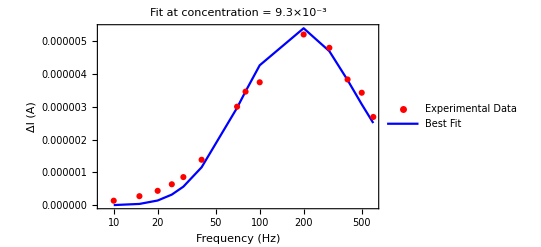

```mathematica
(*Find highest concentration*)
uniqueConcs=DeleteDuplicates[filteredData[[All,2]]];
maxConc=Max[uniqueConcs];

(*Extract data at highest concentration*)
highestConcData=Select[filteredData,#[[2]]==maxConc&];

(*Evaluate model at fitted parameters*)
rct0Fit=result["Rct0"];
rct1Fit=result["Rct1"];
kDFit=result["kD"];
captFit=result["Capt"]
modelCurve=Table[{f,ModelFunction[f,maxConc,Join[constants,<|"Rct0"->rct0Fit,"Rct1"->rct1Fit,"kD"->kDFit, "Capt"->captFit|>]]},{f,Sort[highestConcData[[All,1]]]}];

(*Plot*)
ListLogLinearPlot[{highestConcData[[All,{1,3}]],modelCurve},PlotStyle->{Red,Blue},PlotMarkers->{Automatic,None},Joined->{False,True},PlotLegends->{"Experimental Data","Best Fit"},Frame->True,FrameLabel->{"Frequency (Hz)","ΔI (A)"},PlotLabel->Row[{"Fit at concentration = ",ScientificForm[maxConc]}]]
```

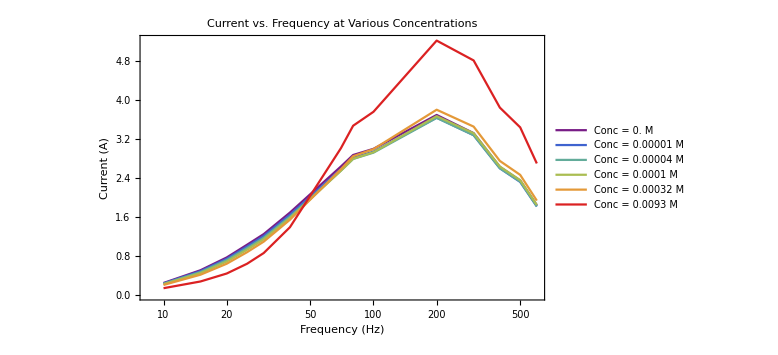

```mathematica
(*Convert association to list*)
datasets=Normal[deltaIwithResistor];

(*Colors*)
colors=ColorData["Rainbow"]/@Rescale[Range[Length[datasets]]];

(*Plot*)
plot=ListLogLinearPlot[datasets[[All,2]],PlotStyle->(Directive[#,Thick]&/@colors),Joined->True,Frame->True,FrameLabel->{"Frequency (Hz)","Current (A)"},PlotLabel->"Current vs. Frequency at Various Concentrations",PlotLegends->Placed[LineLegend[colors,"Conc = "<>ToString[#]<>" M"&/@datasets[[All,1]]],Right],ImageSize->Large];

plot
```

6.59176×10^-7

{411.5,493.8,576.1,658.4,740.7,823.,905.3,987.6,1069.9,1152.2,1234.5,1316.8,1399.1,1481.4,1563.7,1646.,1728.3,1810.6,1892.9,1975.2,2057.5,2139.8,2222.1,2304.4,2386.7,2469.}

5.05929×10^-7

4.62158×10^-6

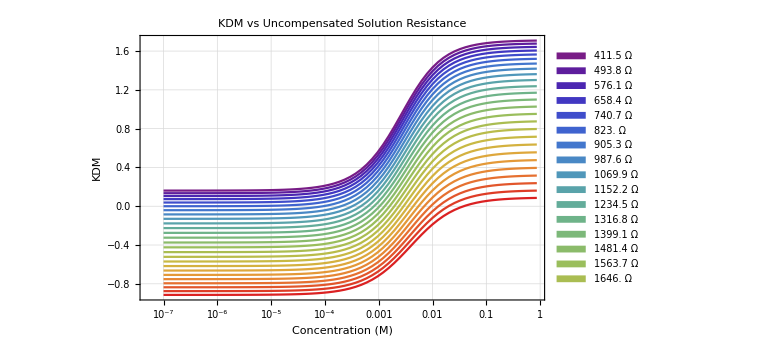

```mathematica
(*--------------------------------------------------------*)
(*PRE-DEFINED VALUES-replace these with your latest fit*)(*--------------------------------------------------------*)(*Your known constants*)
constants=<|"CDL"->4.12335*10^-7,"Capt"->8.71224*10^-7,"Rct0"->4918.21|>;

(*From your fitted result object*)
rct0Fit=result["Rct0"];
rct1Fit=result["Rct1"];
kDFit=result["kD"];
captFit=result["Capt"]
(*Frequencies for KDM calculation*)
fLow=25;
fHigh=200;

inVitroRsol=1571.56;

inVitroRsol = 1000;
inVitroRsol = 150;
inVitroRsol = 823;

(*Rsol values to try*)
(* solValues={inVitroRsol,inVitroRsol*3,inVitroRsol*3*3,inVitroRsol*3*3*3}; *)

(* rsolValues=Join[{inVitroRsol},inVitroRsol*Range[2,20,2]] *)

rsolValues=inVitroRsol+inVitroRsol*Range[-0.5,2,0.1]

(*Range of concentrations*)
concRange=Table[10^x,{x,-7,0,5/49}];

(*Compute reference baseline currents*)

refParams=Join[constants,<|"Rct0"->rct0Fit,"Rct1"->rct1Fit,"kD"->kDFit,"Capt"->captFit,"Rsol"->inVitroRsol|>];
ilow0Ref=ModelFunction[fLow,0,refParams]
ihigh0Ref=ModelFunction[fHigh,0,refParams]

(*Update ComputeKDM to accept ref currents*)
ComputeKDM[conc_,fLow_,fHigh_,params_Association,ilow0Ref_, ihigh0Ref_]:=Module[{ihigh,ilow,normHigh,normLow,kdm},
ihigh=ModelFunction[fHigh,conc,params];
ilow=ModelFunction[fLow,conc,params];
normHigh=ihigh/ihigh0Ref;
normLow=ilow/ilow0Ref;
kdm=(normHigh-normLow)/(0.5*(normHigh+normLow));
kdm];
(*--------------------------------------------------------*)
(*COMPUTE KDM CURVES FOR DIFFERENT Rsol*)
(*--------------------------------------------------------*)
kdms=Table[Module[{color,curve,fullParams,rsol},(*Pick the i-th Rsol value*)
rsol=rsolValues[[i]];
(*Assign color*)
color=ColorData["Rainbow"][Rescale[i,{1,Length[rsolValues]}]];
(*Complete parameter set*)
fullParams=Join[constants,<|"Rct0"->rct0Fit,"Rct1"->rct1Fit,"kD"->kDFit,"Capt"->captFit,"Rsol"->rsol|>];
(*KDM values over concentration range*)
curve=Table[{conc,ComputeKDM[conc,fLow,fHigh,fullParams,ilow0Ref, ihigh0Ref ]},{conc,concRange}];
{color,curve}],{i,Length[rsolValues]}];

(*--------------------------------------------------------*)
(*PLOT ALL KDM CURVES*)
(*--------------------------------------------------------*)

Show[ListLogLinearPlot[kdms[[All,2]],PlotStyle->(Directive[#,Thick]&/@kdms[[All,1]]),Joined->True,PlotLabel->"KDM vs Uncompensated Solution Resistance",Frame->True,FrameLabel->{"Concentration (M)","KDM"},PlotLegends->Placed[SwatchLegend[kdms[[All,1]],ToString[#]<>" Ω"&/@rsolValues],Right],PlotRange->All,ImageSize->Large,GridLines->Automatic,FrameTicksStyle->Directive[FontSize->12]]]
```

All unique concentrations in data: {0.,0.00001,0.00004,0.0001,0.00032,0.0093}

Using these 5 concentrations for KDM plot: {0.,0.00001,0.00004,0.0001,0.00032,0.0093}

KDM points: {{0.,0.},{0.00001,0.00462264},{0.00004,0.0183635},{0.0001,0.0452818},{0.00032,0.137864},{0.0093,1.18848}}

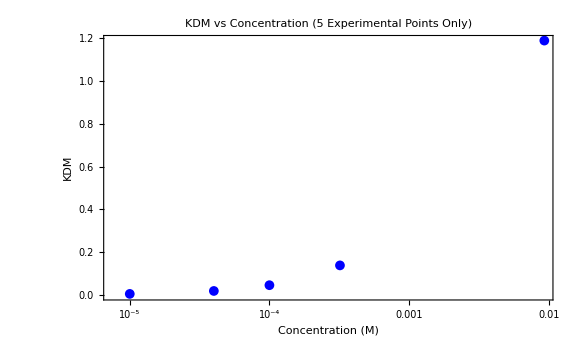

```mathematica
(*--------------------------------------------------------*)(*CONSTANTS AND FITTED PARAMETERS*)(*--------------------------------------------------------*)
(*Constants from your fit*)
constants=<|"CDL"->4.12335*10^-7,"Capt"->8.71224*10^-7,"Rct0"->4918.21|>;

(*Fitted parameters from result object*)
rct0Fit=result["Rct0"];
rct1Fit=result["Rct1"];
kDFit=result["kD"];
captFit=result["Capt"];

(*Frequencies for KDM calculation*)
fLow=25;
fHigh=200;

(*--------------------------------------------------------*)
(*SELECT FIVE EXPERIMENTAL CONCENTRATIONS*)
(*--------------------------------------------------------*)

(*Extract unique experimental concentrations*)
allConcs=Sort[DeleteDuplicates[filteredData[[All,2]]]];
Print["All unique concentrations in data: ",allConcs];

(*Pick first 5 (or fewer if data has fewer than 5)*)
concentrationRange=Take[allConcs,UpTo[10]];

Print["Using these 5 concentrations for KDM plot: ",concentrationRange];

(*--------------------------------------------------------*)
(*COMPUTE REFERENCE BASELINE CURRENTS*)
(*--------------------------------------------------------*)

(*Compute reference currents at C=0*)
refParams=Join[constants,<|"Rct0"->rct0Fit,"Rct1"->rct1Fit,"kD"->kDFit,"Capt"->captFit,"Rsol"->inVitroRsol|>];

ihigh0Ref=ModelFunction[fHigh,0,refParams];
ilow0Ref=ModelFunction[fLow,0,refParams];

(*--------------------------------------------------------*)
(*DEFINE ComputeKDM FUNCTION*)
(*--------------------------------------------------------*)

ComputeKDM[conc_,fLow_,fHigh_,params_Association,ilow0Ref_, ihigh0Ref_]:=Module[{ihigh,ilow,normHigh,normLow,kdm},ihigh=ModelFunction[fHigh,conc,params];
ilow=ModelFunction[fLow,conc,params];
normHigh=ihigh/ihigh0Ref;
normLow=ilow/ilow0Ref;
kdm=(normHigh-normLow)/(0.5*(normHigh+normLow));
kdm];

(*--------------------------------------------------------*)
(*COMPUTE 5 KDM POINTS*)
(*--------------------------------------------------------*)

(*Complete parameter set for fitted values*)
fullParams=Join[constants,<|"Rct0"->rct0Fit,"Rct1"->rct1Fit,"kD"->kDFit,"Capt"->captFit,"Rsol"->inVitroRsol|>];

(*Compute KDM at 5 concentrations*)
kdmPoints=Table[{conc,ComputeKDM[conc,fLow,fHigh,fullParams,ilow0Ref, ihigh0Ref]},{conc,concentrationRange}];

Print["KDM points: ",kdmPoints];

(*--------------------------------------------------------*)
(*PLOT KDM vs CONCENTRATION (5 POINTS ONLY)*)
(*--------------------------------------------------------*)

kdmPlot=ListLogLinearPlot[{kdmPoints},Joined->False,PlotStyle->{Directive[Blue,Thick]},PlotMarkers->{Automatic,Medium},Frame->True,FrameLabel->{"Concentration (M)","KDM"},PlotLabel->"KDM vs Concentration (5 Experimental Points Only)",PlotRange->All,ImageSize->Large,GridLines->Automatic,FrameTicksStyle->Directive[FontSize->12]];

kdmPlot
```

Best-fit kD_effective = 3.47×10^-3

Best-fit KDM_Max = 1.63

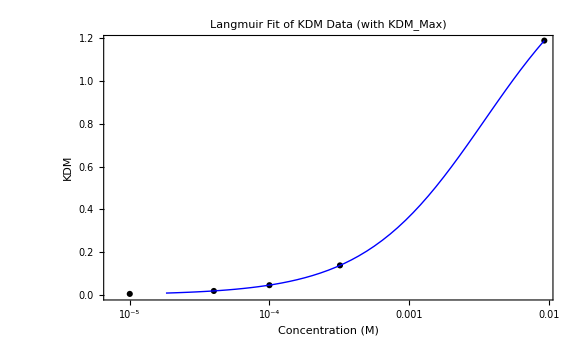

```mathematica
(*-------------------------------------------------------------*)
(*1. PREPARE DATA*)(*-------------------------------------------------------------*)
(*Experimental concentrations*)

(*Compute KDM values for each experimental concentration*)
kdmData=Table[{conc,ComputeKDM[conc,fLow,fHigh,Join[constants,<|"Rct0"->rct0Fit,"Rct1"->rct1Fit,"kD"->kDFit,"Capt"->captFit,"Rsol"->inVitroRsol|>],ilow0Ref, ihigh0Ref]},{conc,concentrationRange}];

(*-------------------------------------------------------------*)
(*2. FIT EXTENDED LANGMUIR MODEL*)
(*-------------------------------------------------------------*)

(*Extended Langmuir model*)
langmuirModel[conc_,kDfit_,kdmMax_]:=kdmMax*conc/(kDfit+conc);

(*Fit both parameters*)
fitResult=FindFit[kdmData,langmuirModel[conc,kDfit,kdmMax],{{kDfit,kDFit,1*^-9,1*^-2},{kdmMax,1,0,10}},conc,Method->"NMinimize"];

Print["Best-fit kD_effective = ",ScientificForm[kDfit/. fitResult,3]];
Print["Best-fit KDM_Max = ",ScientificForm[kdmMax/. fitResult,3]];

(*-------------------------------------------------------------*)
(*3. PLOT DATA AND FIT*)
(*-------------------------------------------------------------*)

Show[
(*Experimental points*)
ListLogLinearPlot[{kdmData},PlotStyle->{Black},PlotMarkers->Automatic,Joined->False,Frame->True,FrameLabel->{"Concentration (M)","KDM"},PlotRange->All,PlotLabel->"Langmuir Fit of KDM Data (with KDM_Max)",ImageSize->Large],

(*Overlay fitted curve*)
LogLinearPlot[langmuirModel[conc,kDfit/. fitResult,kdmMax/. fitResult],{conc,Min[concentrationRange],Max[concentrationRange]},PlotStyle->{Blue,Thick}]
]
```

```mathematica
(*-------------------------------------------------------------*)
kDEffective = kDfit/. fitResult ;
(*1. PREPARE PARAMS WITH Gamma=1*)(*-------------------------------------------------------------*)(*Compute effective Rct under Gamma=1*)(*For Gamma=1,theta=1->RctEff=Rct1*)


inVivoRsol = 1000;
inVivoRsol = inVitroRsol;

rctEffGamma1=rct1Fit;

(*Complete parameter set with Gamma=1 and Rsol=inVitroRsol*)
paramsGamma1=Join[constants,<|"Rct0"->rct0Fit,"Rct1"->rct1Fit,"kD"->kDFit,"Capt"->captFit,"Rsol"->inVivoRsol|>];

(*-------------------------------------------------------------*)
(*2. COMPUTE KDM VS CONCENTRATION*)
(*-------------------------------------------------------------*)
decades=Range[-5,-1,1/5];
concentrationRangeForPlotting=10^decades;
ilow0RefinVivo = ModelFunction[fLow,0,paramsGamma1];
ihigh0RefinVivo= ModelFunction[fHigh,0,paramsGamma1];

kdmGamma1Data=Table[{conc,ComputeKDM[conc,fLow,fHigh,paramsGamma1,ilow0RefinVivo, ihigh0RefinVivo]},{conc,concentrationRangeForPlotting}];

(*-------------------------------------------------------------*)
(*3. PLOT CURVE*)
(*-------------------------------------------------------------*)

ListLogLinearPlot[{kdmGamma1Data},PlotStyle->{Blue,Thick},Joined->False,Frame->True,FrameLabel->{"Concentration (M)","KDM"},PlotLabel->"KDM vs Concentration (Gamma = 1, Rsol = R_inVitro)",PlotRange->All,ImageSize->Large];
```

```mathematica
(*----------------------------------------------------*)(*EXTRACT PARAMETERS FROM YOUR PREVIOUS FIT*)(*----------------------------------------------------*)
kDfitVal= kDfit/. fitResult ;

kdmMaxVal=kdmMax/. fitResult;
Print["Best-fit kD_effective = ",ScientificForm[kDfitVal,3]];
Print["Best-fit KDM_Max = ",ScientificForm[kdmMaxVal,3]];

(*----------------------------------------------------*)
(*INVERSION FUNCTION*)
(*----------------------------------------------------*)

EstimateConcentration[KDMmeasured_,kDeffective_,kdmMax_]:=Module[
{estimatedConc},
If[KDMmeasured>=kdmMax,estimatedConc=Infinity,estimatedConc=(kDeffective*KDMmeasured)/(kdmMax-KDMmeasured)];
estimatedConc
];

(*----------------------------------------------------*)
(*FUNCTION TO COMPUTE ESTIMATES FOR ANY Rsol*)
(*----------------------------------------------------*)

(* we need to be careful.. are we using molecular kD from the global data fit at multiple frequencies? or the kDeffective ? *)

ComputeEstimatesForRsol[RsolVal_]:=Module[{params,kdmGamma1Vals,estimates},(*Define parameter set for this Rsol*)params=Join[constants,<|"Rct0"->rct0Fit,"Rct1"->rct1Fit,"kD"->kDFit,"Capt"->captFit,"Rsol"->RsolVal|>];

kdmGamma1Vals=Table[{conc,ComputeKDM[conc,fLow,fHigh,params,ilow0RefinVivo, ihigh0RefinVivo]},{conc,kdmGamma1Data[[All,1]]}];
(*Estimate concentrations from KDMs*)
estimates=Table[
Module[
{trueConc=kdmGamma1Vals[[i,1]],KDMmeasured=kdmGamma1Vals[[i,2]],estimatedConc,percentError},
estimatedConc=EstimateConcentration[KDMmeasured,kDEffective,kdmMaxVal];
percentError=If[trueConc==0,Indeterminate,100*(estimatedConc-trueConc)/trueConc];
{trueConc,KDMmeasured,estimatedConc,percentError}],{i,Length[kdmGamma1Vals]}
];
Return[estimates];];

(*----------------------------------------------------*)
(*RUN FOR THREE Rsol VALUES*)
(*----------------------------------------------------*)

baselineRsol=inVivoRsol
rsolOffsets={-200, -100, 0,+100,+200};
rsolLabels={"Rsol - 200 Ω","Rsol - 100 Ω","1571 Ω (baseline)", "Rsol + 100 Ω", "Rsol + 200 Ω"};
(*Generate labels*)
rsolLabels=Table[Module[{rsolValStr},rsolValStr=ToString[Round[baselineRsol+offset]];
If[offset==0,rsolValStr<>" Ω (baseline)",rsolValStr<>" Ω"]],{offset,rsolOffsets}]

allResults=Table[ComputeEstimatesForRsol[baselineRsol+offset],{offset,rsolOffsets}];

(*----------------------------------------------------*)
(*DISPLAY RESULTS*)
(*----------------------------------------------------*)

Print["\nComparison of True vs Estimated Concentrations for different Rsol:\n"];

Do[Print[Style[rsolLabels[[idx]],Bold,Blue]];
Print[Grid[Prepend[allResults[[idx]],{"True Conc (M)","Measured KDM","Estimated Conc (M)","Percent Error"}],Frame->All]];
Print["\n"];,{idx,Length[rsolLabels]}];
```

Best-fit kD_effective = 3.47×10^-3

Best-fit KDM_Max = 1.63

823

{623 Ω,723 Ω,823 Ω (baseline),923 Ω,1023 Ω}

Comparison of True vs Estimated Concentrations for different Rsol:

623 Ω

True Conc (M) | Measured KDM | Estimated Conc (M) | Percent Error
1/100000 | 0.0921794 | 0.000207882 | 1978.82
1/(10000 10^(4/5)) | 0.0950188 | 0.000214681 | 1254.55
1/(10000 10^(3/5)) | 0.099503 | 0.00022547 | 797.613
1/(10000 10^(2/5)) | 0.10657 | 0.000242603 | 509.391
1/(10000 10^(1/5)) | 0.117672 | 0.000269838 | 327.664
1/10000 | 0.135019 | 0.000313206 | 213.206
1/(1000 10^(4/5)) | 0.161905 | 0.000382441 | 141.304
1/(1000 10^(3/5)) | 0.203034 | 0.000493393 | 96.4232
1/(1000 10^(2/5)) | 0.264671 | 0.000672162 | 68.8395
1/(1000 10^(1/5)) | 0.354131 | 0.0009623 | 52.5142
1/1000 | 0.477779 | 0.00143733 | 43.7333
1/(100 10^(4/5)) | 0.636853 | 0.00222203 | 40.2008
1/(100 10^(3/5)) | 0.822353 | 0.00352636 | 40.3868
1/(100 10^(2/5)) | 1.01393 | 0.00569478 | 43.0465
1/(100 10^(1/5)) | 1.18749 | 0.00927158 | 46.9446
1/100 | 1.32684 | 0.0150848 | 50.8483
1/(10 10^(4/5)) | 1.42864 | 0.024359 | 53.695
1/(10 10^(3/5)) | 1.49842 | 0.03886 | 54.7043
1/(10 10^(2/5)) | 1.54446 | 0.0610363 | 53.3162
1/(10 10^(1/5)) | 1.57421 | 0.0940413 | 49.0454
1/10 | 1.59322 | 0.141407 | 41.4074

723 Ω

True Conc (M) | Measured KDM | Estimated Conc (M) | Percent Error
1/100000 | 0.0506849 | 0.000111305 | 1013.05
1/(10000 10^(4/5)) | 0.053452 | 0.000117588 | 641.928
1/(10000 10^(3/5)) | 0.0578222 | 0.000127555 | 407.804
1/(10000 10^(2/5)) | 0.0647099 | 0.000143376 | 260.144
1/(10000 10^(1/5)) | 0.0755303 | 0.000168514 | 167.076
1/10000 | 0.0924411 | 0.000208508 | 108.508
1/(1000 10^(4/5)) | 0.118655 | 0.000272271 | 71.7911
1/(1000 10^(3/5)) | 0.15877 | 0.000374236 | 48.9859
1/(1000 10^(2/5)) | 0.21892 | 0.000537977 | 35.1337
1/(1000 10^(1/5)) | 0.306308 | 0.000802329 | 27.1606
1/1000 | 0.427291 | 0.00123159 | 23.1591
1/(100 10^(4/5)) | 0.583365 | 0.00193162 | 21.8772
1/(100 10^(3/5)) | 0.766161 | 0.00307227 | 22.3091
1/(100 10^(2/5)) | 0.95614 | 0.00491123 | 23.3645
1/(100 10^(1/5)) | 1.12965 | 0.00780513 | 23.703
1/100 | 1.27023 | 0.0121838 | 21.8383
1/(10 10^(4/5)) | 1.37386 | 0.018461 | 16.481
1/(10 10^(3/5)) | 1.44546 | 0.0268634 | 6.9452
1/(10 10^(2/5)) | 1.49299 | 0.0372109 | -6.53044
1/(10 10^(1/5)) | 1.52385 | 0.0487793 | -22.6899
1/10 | 1.54363 | 0.0604275 | -39.5725

823 Ω (baseline)

True Conc (M) | Measured KDM | Estimated Conc (M) | Percent Error
1/100000 | 0.00462264 | 9.86418×10^-6 | -1.35822
1/(10000 10^(4/5)) | 0.00731654 | 0.0000156385 | -1.32762
1/(10000 10^(3/5)) | 0.0115712 | 0.0000247975 | -1.27933
1/(10000 10^(2/5)) | 0.0182774 | 0.0000393317 | -1.20332
1/(10000 10^(1/5)) | 0.0288133 | 0.0000624117 | -1.08415
1/10000 | 0.0452818 | 0.0000991015 | -0.898523
1/(1000 10^(4/5)) | 0.0708161 | 0.000157519 | -0.61231
1/(1000 10^(3/5)) | 0.109904 | 0.000250741 | -0.178175
1/(1000 10^(2/5)) | 0.168553 | 0.000399951 | 0.463179
1/(1000 10^(1/5)) | 0.253845 | 0.000639606 | 1.37069
1/1000 | 0.37213 | 0.00102565 | 2.56523
1/(100 10^(4/5)) | 0.525154 | 0.00164746 | 3.94741
1/(100 10^(3/5)) | 0.705162 | 0.00264164 | 5.1654
1/(100 10^(2/5)) | 0.893414 | 0.0041995 | 5.48658
1/(100 10^(1/5)) | 1.06671 | 0.00655028 | 3.81501
1/100 | 1.20838 | 0.0098996 | -1.00396
1/(10 10^(4/5)) | 1.31372 | 0.0143204 | -9.64422
1/(10 10^(3/5)) | 1.38704 | 0.0196387 | -21.8168
1/(10 10^(2/5)) | 1.43601 | 0.0254033 | -36.1898
1/(10 10^(1/5)) | 1.46794 | 0.0310106 | -50.8515
1/10 | 1.48847 | 0.0359307 | -64.0693

923 Ω

True Conc (M) | Measured KDM | Estimated Conc (M) | Percent Error
1/100000 | -0.0456255 | -0.0000944439 | -1044.44
1/(10000 10^(4/5)) | -0.0430061 | -0.000089161 | -662.568
1/(10000 10^(3/5)) | -0.0388689 | -0.0000807832 | -421.604
1/(10000 10^(2/5)) | -0.0323476 | -0.000067493 | -269.535
1/(10000 10^(1/5)) | -0.0221011 | -0.0000463993 | -173.538
1/10000 | -0.00608254 | -0.0000128946 | -112.895
1/(1000 10^(4/5)) | 0.01876 | 0.0000403824 | -74.5204
1/(1000 10^(3/5)) | 0.0568044 | 0.000125228 | -50.1457
1/(1000 10^(2/5)) | 0.113923 | 0.000260597 | -34.541
1/(1000 10^(1/5)) | 0.197079 | 0.000476935 | -24.4108
1/1000 | 0.312605 | 0.000822732 | -17.7268
1/(100 10^(4/5)) | 0.462484 | 0.00137313 | -13.3611
1/(100 10^(3/5)) | 0.639562 | 0.00223758 | -10.9205
1/(100 10^(2/5)) | 0.825889 | 0.00355704 | -10.6511
1/(100 10^(1/5)) | 0.998745 | 0.00547503 | -13.2266
1/100 | 1.14126 | 0.00807195 | -19.2805
1/(10 10^(4/5)) | 1.24812 | 0.0112826 | -28.8114
1/(10 10^(3/5)) | 1.32303 | 0.0148565 | -40.8553
1/(10 10^(2/5)) | 1.37336 | 0.0184179 | -53.7363
1/(10 10^(1/5)) | 1.4063 | 0.0216082 | -65.7533
1/10 | 1.42755 | 0.02421 | -75.79

1023 Ω

True Conc (M) | Measured KDM | Estimated Conc (M) | Percent Error
1/100000 | -0.0994106 | -0.000199387 | -2093.87
1/(10000 10^(4/5)) | -0.0968672 | -0.000194572 | -1327.66
1/(10000 10^(3/5)) | -0.09285 | -0.000186937 | -844.208
1/(10000 10^(2/5)) | -0.0865174 | -0.000174829 | -539.15
1/(10000 10^(1/5)) | -0.0765664 | -0.000155621 | -346.643
1/10000 | -0.0610075 | -0.000125137 | -225.137
1/(1000 10^(4/5)) | -0.0368718 | -0.0000767241 | -148.41
1/(1000 10^(3/5)) | 0.000105071 | 2.23588×10^-7 | -99.911
1/(1000 10^(2/5)) | 0.0556576 | 0.000122611 | -69.2015
1/(1000 10^(1/5)) | 0.136621 | 0.000317262 | -49.7174
1/1000 | 0.2493 | 0.000626088 | -37.3912
1/(100 10^(4/5)) | 0.395896 | 0.00111213 | -29.8294
1/(100 10^(3/5)) | 0.569838 | 0.00186281 | -25.8401
1/(100 10^(2/5)) | 0.753961 | 0.00298135 | -25.1119
1/(100 10^(1/5)) | 0.926052 | 0.00455406 | -27.8231
1/100 | 1.06911 | 0.00659295 | -34.0705
1/(10 10^(4/5)) | 1.17722 | 0.00898415 | -43.3139
1/(10 10^(3/5)) | 1.25355 | 0.0114941 | -54.2413
1/(10 10^(2/5)) | 1.30509 | 0.0138514 | -65.2069
1/(10 10^(1/5)) | 1.33897 | 0.0158518 | -74.8766
1/10 | 1.36087 | 0.0174113 | -82.5887

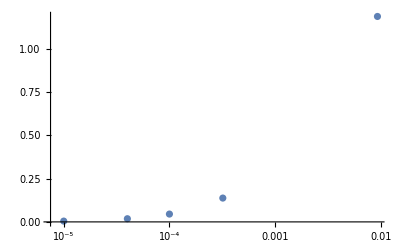

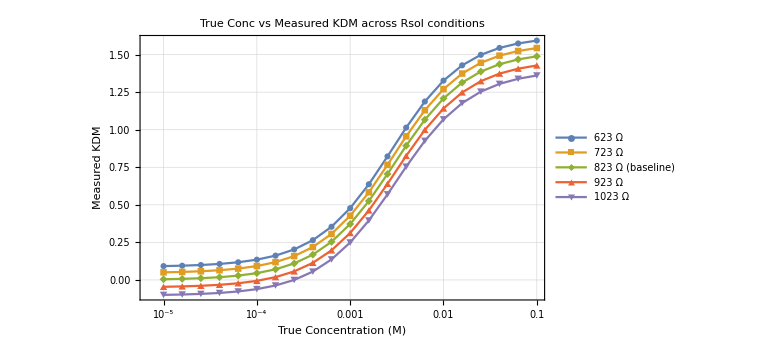

```mathematica
(*-----------------------------------------------------------*)
(*Prepare plot data for TrueConc vs Measured KDM*)(*-----------------------------------------------------------*)(*Each element of allResults is a list of rows:{TrueConc,KDMmeasured,EstimatedConc,PercentError}*)(*Extract {TrueConc,KDMmeasured} pairs for each Rsol group*)curveData=allResults[[All,All,{1,2}]];

(*-----------------------------------------------------------*)
(*Plot all curves together*)
(*-----------------------------------------------------------*)
ListLogLinearPlot[kdmData]
ListLogLinearPlot[curveData,Joined->True,PlotMarkers->Automatic,PlotStyle->Automatic,Frame->True,FrameLabel->{"True Concentration (M)","Measured KDM"},PlotLabel->"True Conc vs Measured KDM across Rsol conditions",PlotLegends->Placed[rsolLabels,Right],ImageSize->Large,GridLines->Automatic]
```

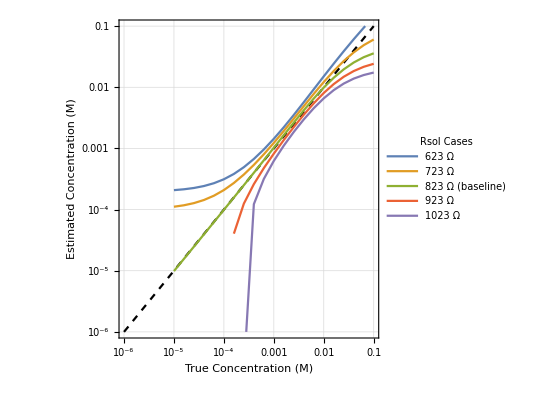

```mathematica
(*----------------------------------------------------*)(*PREPARE DATA FOR PLOTTING*)(*----------------------------------------------------*)(*Extract {trueConc,estimatedConc} pairs for each Rsol offset*)
plotDataSets=allResults[[All,All,{1,3}]];

(*Compute min and max concentration for axis limits*)
allConcVals=Flatten[plotDataSets[[All,All,1]]];
maxConc=Max[allConcVals];
minConc=Max[Min[Select[allConcVals,#>0&]]/10,10^-9];

(*Build the 1:1 line as a function plot*)
oneToOnePlot=LogLogPlot[x,{x,minConc,maxConc},PlotStyle->{Black,Dashed},PlotLegends->None, Frame->True,FrameLabel->{"True Concentration (M)","Estimated Concentration (M)"}, AspectRatio->1, GridLines->True];

(*Create the scatter plots for all Rsol datasets*)
scatterPlots=ListLogLogPlot[plotDataSets,Joined->True,PlotMarkers->None,Frame->True,FrameLabel->{"True Concentration (M)","Estimated Concentration (M)"},PlotRange->{{minConc,maxConc},{minConc,maxConc}},AspectRatio->1,PlotLegends->Placed[LineLegend[rsolLabels,LegendLabel->"Rsol Cases"],Right],PlotLabel->"Estimated vs True Concentration for Different Rsol",ImageSize->Large];

(*Combine plots*)
finalPlot=Show[oneToOnePlot, scatterPlots ];

finalPlot
```

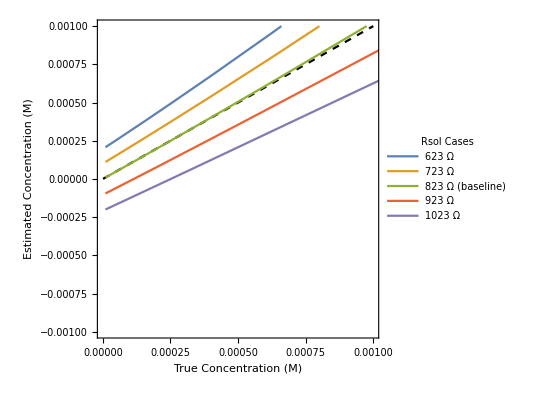

```mathematica
(*Build the 1:1 line as a function plot*)
linearPlotRange = {{0,0.001}, {-0.001,0.001}};
oneToOnePlot2=Plot[x,{x,minConc,maxConc},PlotStyle->{Black,Dashed},PlotLegends->None, Frame->True,FrameLabel->{"True Concentration (M)","Estimated Concentration (M)"}, AspectRatio->1, PlotRange->linearPlotRange];

(*Create the scatter plots for all Rsol datasets*)
scatterPlots2=ListPlot[plotDataSets,Joined->True,PlotMarkers->None,Frame->True,FrameLabel->{"True Concentration (M)","Estimated Concentration (M)"},PlotRange->linearPlotRange,AspectRatio->1,PlotLegends->Placed[LineLegend[rsolLabels,LegendLabel->"Rsol Cases"],Right],PlotLabel->"Estimated vs True Concentration for Different Rsol",ImageSize->Large];

(*Combine plots*)
finalPlot2=Show[oneToOnePlot2, scatterPlots2 ];

finalPlot2
```

{{0,0.001},{0,0.001}}

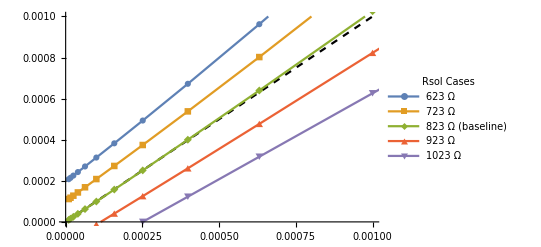

```mathematica
(*Build the 1:1 line as a function plot*)
ClarkeErrorPlotRange={{0,0.001},{0,0.001}}
oneToOnePlot=Plot[x,{x,minConc,maxConc},PlotStyle->{Black,Dashed},PlotLegends->None, PlotRange->ClarkeErrorPlotRange];

(*Create the scatter plots for all Rsol datasets*)
scatterPlots=ListPlot[plotDataSets,Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{"True Concentration (M)","Estimated Concentration (M)"},FrameTicksStyle->Directive[FontSize->12],PlotRange->ClarkeErrorPlotRange,AspectRatio->1,PlotLegends->Placed[LineLegend[rsolLabels,LegendLabel->"Rsol Cases"],Right],PlotLabel->"Estimated vs True Concentration for Different Rsol",ImageSize->Large];

(*Combine plots*)
finalPlot=Show[oneToOnePlot,scatterPlots];

finalPlot
```

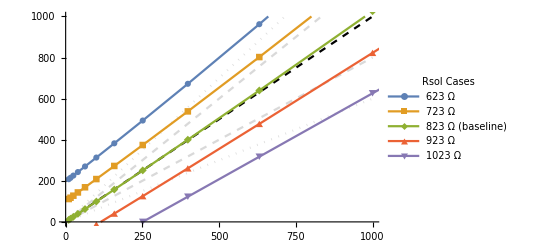

```mathematica
(*--------------------------------------------------------*)(*Convert data from M->µM*)(*--------------------------------------------------------*)plotDataSetsMicroMolar=Map[#*10^6&,plotDataSets,{3}];

(*Plot range in µM*)
ClarkeErrorPlotRangeMicroMolar={{0,1000},{0,1000}};

(*1:1 line in µM*)
oneToOnePlot=Plot[x,{x,0,1000},PlotStyle->{Black,Dashed,Thick},PlotLegends->None,PlotRange->ClarkeErrorPlotRangeMicroMolar];

(*Error lines (+/-20%,+/-40%)*)
errorLines=Plot[{1.2*x,0.8*x,1.4*x,0.6*x},{x,0,1000},PlotStyle->{Directive[LightGray,Dashed,Medium],Directive[LightGray,Dashed,Medium],Directive[LightGray,Dotted,Medium],Directive[LightGray,Dotted,Medium]},PlotRange->ClarkeErrorPlotRangeMicroMolar,PlotLegends->None];

(*Scatter plots in µM*)
scatterPlots=ListPlot[plotDataSetsMicroMolar,Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{"True Concentration (µM)","Estimated Concentration (µM)"},FrameTicksStyle->Directive[FontSize->12],PlotRange->ClarkeErrorPlotRangeMicroMolar,AspectRatio->1,PlotLegends->Placed[LineLegend[rsolLabels,LegendLabel->"Rsol Cases"],Right],PlotLabel->"Estimated vs True Concentration for Different Rsol (µM)",ImageSize->Large];

(*Combine plots*)
finalPlot=Show[oneToOnePlot,errorLines,scatterPlots];

finalPlot
```

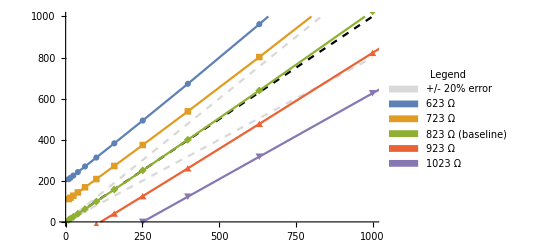

```mathematica
(*--------------------------------------------------------*)(*Convert data from M->µM*)(*--------------------------------------------------------*)plotDataSetsMicroMolar=Map[#*10^6&,plotDataSets,{3}];

(*Plot range in µM*)
ClarkeErrorPlotRangeMicroMolar={{0,1000},{0,1000}};

(*1:1 line in µM*)
oneToOnePlot=Plot[x,{x,0,1000},PlotStyle->{Black,Dashed,Thick},PlotLegends->None,PlotRange->ClarkeErrorPlotRangeMicroMolar];

(*Error lines (+/-10%,+/-20%)*)
errorLines=Plot[{1.20 x,0.80 x     (*±20%*)},{x,0,1000},PlotStyle->{Directive[LightGray,Dashed,Medium],Directive[LightGray,Dashed,Medium],Directive[LightGray,Dotted,Medium],Directive[LightGray,Dotted,Medium]},PlotRange->ClarkeErrorPlotRangeMicroMolar,PlotLegends->None];



(*--------------------------------------------------------*)
(*Assemble the combined legend*)
(*--------------------------------------------------------*)

(*Legend items for the guideline lines*)
guidelineStyles={Directive[LightGray,Dashed,Medium]};

guidelineLabels={"+/- 20% error"};

(*Create legends separately*)
legendGuidelines=LineLegend[guidelineStyles,guidelineLabels,LegendLabel->"Guidelines"];

legendRsol=LineLegend[rsolLabels,LegendLabel->"Rsol Cases"];

(*Combine them*)
combinedLegend=SwatchLegend[Join[guidelineStyles,ColorData[97]/@Range[Length[rsolLabels]]],Join[guidelineLabels,rsolLabels],LegendLabel->"Legend"];

(*Alternatively,if you want separate boxes:*)
(*combinedLegend=Column[{legendGuidelines,legendRsol}];*)

(*Scatter plots in µM*)
scatterPlots=ListPlot[plotDataSetsMicroMolar,Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{"True Concentration (µM)","Estimated Concentration (µM)"},FrameTicksStyle->Directive[FontSize->12],PlotRange->ClarkeErrorPlotRangeMicroMolar,AspectRatio->1,PlotLegends->combinedLegend,PlotLabel->"Estimated vs True Concentration for Different Rsol (µM)",ImageSize->Large];
(*Combine plots*)
finalPlot=Show[oneToOnePlot,errorLines,scatterPlots,PlotRange->ClarkeErrorPlotRangeMicroMolar];

finalPlot
```

<|CDL→4.12335×10^-7,Rsol→1571.56,Rct0→7471.47,Rct1→3259.43,kD→0.00526958,Capt→6.59176×10^-7|>

<|CDL→4.12335×10^-7,Rsol→823,Rct0→74714.7,Rct1→32594.3,kD→0.00526958,Capt→6.59176×10^-8|>

<|CDL→4.12335×10^-7,Rsol→823,Rct0→37357.3,Rct1→16297.1,kD→0.00526958,Capt→1.31835×10^-7|>

<|CDL→4.12335×10^-7,Rsol→823,Rct0→24904.9,Rct1→10864.8,kD→0.00526958,Capt→1.97753×10^-7|>

<|CDL→4.12335×10^-7,Rsol→823,Rct0→18678.7,Rct1→8148.57,kD→0.00526958,Capt→2.63671×10^-7|>

<|CDL→4.12335×10^-7,Rsol→823,Rct0→14942.9,Rct1→6518.85,kD→0.00526958,Capt→3.29588×10^-7|>

<|CDL→4.12335×10^-7,Rsol→823,Rct0→12452.4,Rct1→5432.38,kD→0.00526958,Capt→3.95506×10^-7|>

<|CDL→4.12335×10^-7,Rsol→823,Rct0→10673.5,Rct1→4656.32,kD→0.00526958,Capt→4.61423×10^-7|>

<|CDL→4.12335×10^-7,Rsol→823,Rct0→9339.33,Rct1→4074.28,kD→0.00526958,Capt→5.27341×10^-7|>

<|CDL→4.12335×10^-7,Rsol→823,Rct0→8301.63,Rct1→3621.59,kD→0.00526958,Capt→5.93259×10^-7|>

<|CDL→4.12335×10^-7,Rsol→823,Rct0→7471.47,Rct1→3259.43,kD→0.00526958,Capt→6.59176×10^-7|>

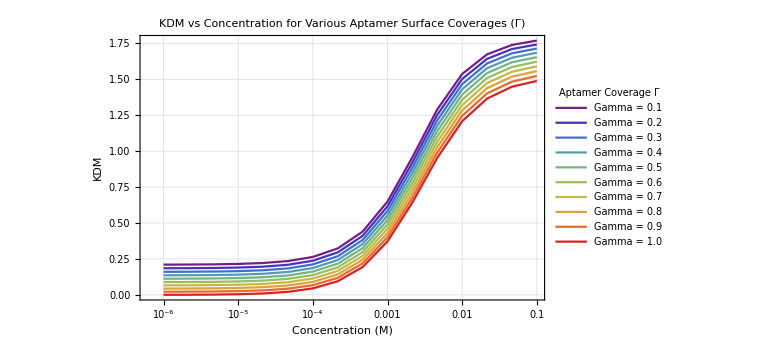

```mathematica
(*------------------------------------------------------------*)(*1. BASELINE PARAMETERS*)(*------------------------------------------------------------*)(*Substitute your fitted values*)
rct0Baseline=result["Rct0"];
rct1Baseline=result["Rct1"];
captBaseline=result["Capt"];
kDFit=result["kD"];
result
(*Rsol*)
RsolBaseline=inVitroRsol;
RsolBaseline=inVivoRsol;
(*Constants association*)
constants=<|"CDL"->result["CDL"],"Rsol"->inVivoRsol|>;

(*Concentration range for plotting*)
decades=Range[-6,-1,1/3];
concentrationRange=10^decades;

(*------------------------------------------------------------*)
(*3. SWEEP GAMMA VALUES*)
(*------------------------------------------------------------*)

gammaValues=Range[0.1,1.0,0.1];

kdmsGammaCurves=Table[
(*Update Rct and Capt for this Gamma*)
rct0Eff=rct0Baseline/gamma;
rct1Eff=rct1Baseline/gamma;
captEff=captBaseline*gamma;

(*Assemble parameter set*)
paramsGamma=Join[constants,<|"Rct0"->rct0Eff,"Rct1"->rct1Eff,"kD"->kDFit,"Capt"->captEff|>];
Print[paramsGamma];
(*Compute KDM across concentration range*)
curve=Table[{conc,ComputeKDM[conc,fLow,fHigh,paramsGamma,ilow0RefinVivo, ihigh0RefinVivo]},{conc,concentrationRange}];
curve,{gamma,gammaValues}];

(*------------------------------------------------------------*)
(*4. PREPARE PLOTTING STYLES*)
(*------------------------------------------------------------*)

(*One color per gamma*)
colors=ColorData["Rainbow"]/@Rescale[Range[Length[gammaValues]]];

legendLabels=("Gamma = "<>ToString[NumberForm[#,{2,1}]])&/@gammaValues;

(*------------------------------------------------------------*)
(*5. PLOT EVERYTHING IN A SINGLE LISTLOGLINEARPLOT*)
(*------------------------------------------------------------*)

finalPlot=ListLogLinearPlot[kdmsGammaCurves,PlotStyle->(Directive[#,Thick]&/@colors),Joined->True,Frame->True,FrameLabel->{"Concentration (M)","KDM"},PlotLegends->Placed[LineLegend[colors,legendLabels,LegendLabel->"Aptamer Coverage Γ"],Right],GridLines->Automatic,ImageSize->Large,PlotLabel->"KDM vs Concentration for Various Aptamer Surface Coverages (Γ)"];

finalPlot
```

```mathematica
gammaLabels=("Gamma = "<>ToString[NumberForm[#,{2,1}]])&/@gammaValues;
kDfitVal= kDfit/. fitResult  (* the effective kD *)

allResultsGamma=Table[(*Update Rct and Capt for this Gamma*)
rct0Eff=rct0Baseline/gamma;
rct1Eff=rct1Baseline/gamma;
captEff=captBaseline*gamma;
paramsGamma=Join[constants,<|"Rct0"->rct0Eff,"Rct1"->rct1Eff,"kD"->kDFit,"Capt"->captEff|>];

(*Compute KDMs for all concentrations*)
kdmGammaVals=Table[{conc,ComputeKDM[conc,fLow,fHigh,paramsGamma,ilow0RefinVivo,ihigh0RefinVivo]},{conc,concentrationRange}];
(*For each KDM,estimate concentration*)estimates=Table[Module[{trueConc=kdmGammaVals[[i,1]],KDMmeasured=kdmGammaVals[[i,2]],estimatedConc,percentError},estimatedConc=EstimateConcentration[KDMmeasured,kDEffective,kdmMaxVal];
percentError=If[trueConc==0,Indeterminate,100*(estimatedConc-trueConc)/trueConc];
{trueConc,KDMmeasured,estimatedConc,percentError}],{i,Length[kdmGammaVals]}];
estimates,{gamma,gammaValues}];

(*------------------------------------------------------------*)
(*DISPLAY RESULTS*)
(*------------------------------------------------------------*)

Print["\nComparison of True vs Estimated Concentrations for different Γ:\n"];

Do[Print[Style[gammaLabels[[idx]],Bold,Blue]];
Print[Grid[Prepend[allResultsGamma[[idx]],{"True Conc (M)","Measured KDM","Estimated Conc (M)","Percent Error"}],Frame->All]];
Print["\n"];,{idx,Length[gammaLabels]}];
```

0.00347339

Comparison of True vs Estimated Concentrations for different Γ:

Gamma = 0.1

True Conc (M) | Measured KDM | Estimated Conc (M) | Percent Error
1/1000000 | 0.210479 | 0.000514164 | 51316.4
1/(100000 10^(2/3)) | 0.211117 | 0.000515954 | 23848.4
1/(100000 10^(1/3)) | 0.21249 | 0.000519812 | 11099.
1/100000 | 0.215443 | 0.000528133 | 5181.33
1/(10000 10^(2/3)) | 0.221779 | 0.000546108 | 2434.81
1/(10000 10^(1/3)) | 0.235313 | 0.000585045 | 1160.44
1/10000 | 0.263931 | 0.00066992 | 569.92
1/(1000 10^(2/3)) | 0.323152 | 0.00085734 | 297.942
1/(1000 10^(1/3)) | 0.440113 | 0.00128219 | 176.24
1/1000 | 0.649403 | 0.00229475 | 129.475
1/(100 10^(2/3)) | 0.958056 | 0.00493505 | 129.065
1/(100 10^(1/3)) | 1.29037 | 0.0131057 | 182.355
1/100 | 1.53679 | 0.0558559 | 458.559
1/(10 10^(2/3)) | 1.67332 | ∞ | ∞
1/(10 10^(1/3)) | 1.73895 | ∞ | ∞
1/10 | 1.76925 | ∞ | ∞

Gamma = 0.2

True Conc (M) | Measured KDM | Estimated Conc (M) | Percent Error
1/1000000 | 0.185236 | 0.000444606 | 44360.6
1/(100000 10^(2/3)) | 0.185862 | 0.000446301 | 20615.4
1/(100000 10^(1/3)) | 0.187209 | 0.000449953 | 9593.95
1/100000 | 0.190105 | 0.000457831 | 4478.31
1/(10000 10^(2/3)) | 0.196319 | 0.000474844 | 2104.03
1/(10000 10^(1/3)) | 0.209594 | 0.000511681 | 1002.38
1/10000 | 0.237667 | 0.000591895 | 491.895
1/(1000 10^(2/3)) | 0.295776 | 0.000768636 | 256.769
1/(1000 10^(1/3)) | 0.410615 | 0.00116737 | 151.503
1/1000 | 0.616465 | 0.00210773 | 110.773
1/(100 10^(2/3)) | 0.921372 | 0.00450122 | 108.928
1/(100 10^(1/3)) | 1.25267 | 0.0114596 | 146.891
1/100 | 1.50187 | 0.0399778 | 299.778
1/(10 10^(2/3)) | 1.64213 | ∞ | ∞
1/(10 10^(1/3)) | 1.71043 | ∞ | ∞
1/10 | 1.7422 | ∞ | ∞

Gamma = 0.3

True Conc (M) | Measured KDM | Estimated Conc (M) | Percent Error
1/1000000 | 0.16049 | 0.000378734 | 37773.4
1/(100000 10^(2/3)) | 0.161104 | 0.00038034 | 17553.8
1/(100000 10^(1/3)) | 0.162424 | 0.000383802 | 8168.77
1/100000 | 0.165265 | 0.00039127 | 3812.7
1/(10000 10^(2/3)) | 0.171359 | 0.000407392 | 1790.94
1/(10000 10^(1/3)) | 0.184378 | 0.000442284 | 852.872
1/10000 | 0.211914 | 0.000518191 | 418.191
1/(1000 10^(2/3)) | 0.268923 | 0.000685092 | 217.991
1/(1000 10^(1/3)) | 0.381658 | 0.00105993 | 128.354
1/1000 | 0.584054 | 0.00193518 | 93.5179
1/(100 10^(2/3)) | 0.885061 | 0.00411372 | 90.9421
1/(100 10^(1/3)) | 1.21493 | 0.0101093 | 117.798
1/100 | 1.46637 | 0.0306847 | 206.847
1/(10 10^(2/3)) | 1.60999 | 0.250079 | 1060.77
1/(10 10^(1/3)) | 1.68076 | ∞ | ∞
1/10 | 1.71393 | ∞ | ∞

Gamma = 0.4

True Conc (M) | Measured KDM | Estimated Conc (M) | Percent Error
1/1000000 | 0.136232 | 0.000316276 | 31527.6
1/(100000 10^(2/3)) | 0.136834 | 0.000317801 | 14651.
1/(100000 10^(1/3)) | 0.138129 | 0.000321087 | 6817.61
1/100000 | 0.140914 | 0.000328173 | 3181.73
1/(10000 10^(2/3)) | 0.146891 | 0.000343468 | 1494.24
1/(10000 10^(1/3)) | 0.159658 | 0.000376558 | 711.269
1/10000 | 0.186664 | 0.000448476 | 348.476
1/(1000 10^(2/3)) | 0.242589 | 0.000606293 | 181.416
1/(1000 10^(1/3)) | 0.353236 | 0.000959197 | 106.653
1/1000 | 0.552175 | 0.00177555 | 77.5554
1/(100 10^(2/3)) | 0.849147 | 0.00376582 | 74.7937
1/(100 10^(1/3)) | 1.17719 | 0.0089832 | 93.5371
1/100 | 1.43037 | 0.0245975 | 145.975
1/(10 10^(2/3)) | 1.57699 | 0.0989384 | 359.231
1/(10 10^(1/3)) | 1.65003 | ∞ | ∞
1/10 | 1.6845 | ∞ | ∞

Gamma = 0.5

True Conc (M) | Measured KDM | Estimated Conc (M) | Percent Error
1/1000000 | 0.112455 | 0.00025699 | 25599.
1/(100000 10^(2/3)) | 0.113045 | 0.000258438 | 11895.6
1/(100000 10^(1/3)) | 0.114315 | 0.00026156 | 5535.14
1/100000 | 0.117046 | 0.000268292 | 2582.92
1/(10000 10^(2/3)) | 0.122906 | 0.000282819 | 1212.73
1/(10000 10^(1/3)) | 0.135426 | 0.000314235 | 576.998
1/10000 | 0.16191 | 0.000382454 | 282.454
1/(1000 10^(2/3)) | 0.216764 | 0.000531868 | 146.871
1/(1000 10^(1/3)) | 0.325346 | 0.000864611 | 86.2749
1/1000 | 0.520829 | 0.00162753 | 62.7531
1/(100 10^(2/3)) | 0.813654 | 0.00345198 | 60.2265
1/(100 10^(1/3)) | 1.13952 | 0.00803112 | 73.0252
1/100 | 1.39397 | 0.0203105 | 103.105
1/(10 10^(2/3)) | 1.54321 | 0.0601327 | 179.111
1/(10 10^(1/3)) | 1.61832 | 0.400574 | 763.011
1/10 | 1.654 | ∞ | ∞

Gamma = 0.6

True Conc (M) | Measured KDM | Estimated Conc (M) | Percent Error
1/1000000 | 0.0891483 | 0.000200652 | 19965.2
1/(100000 10^(2/3)) | 0.0897268 | 0.000202029 | 9277.37
1/(100000 10^(1/3)) | 0.090972 | 0.000204998 | 4316.56
1/100000 | 0.0936498 | 0.0002114 | 2014.
1/(10000 10^(2/3)) | 0.0993963 | 0.000225213 | 945.345
1/(10000 10^(1/3)) | 0.111673 | 0.000255071 | 449.534
1/10000 | 0.137644 | 0.000319854 | 219.854
1/(1000 10^(2/3)) | 0.191443 | 0.000461483 | 114.201
1/(1000 10^(1/3)) | 0.297983 | 0.000775653 | 67.1094
1/1000 | 0.49002 | 0.00148996 | 48.9956
1/(100 10^(2/3)) | 0.778602 | 0.00316765 | 47.0292
1/(100 10^(1/3)) | 1.10197 | 0.00721667 | 55.4783
1/100 | 1.35723 | 0.0171345 | 71.345
1/(10 10^(2/3)) | 1.50875 | 0.0423974 | 96.7914
1/(10 10^(1/3)) | 1.58573 | 0.118135 | 154.515
1/10 | 1.62252 | 0.572874 | 472.874

Gamma = 0.7

True Conc (M) | Measured KDM | Estimated Conc (M) | Percent Error
1/1000000 | 0.0663048 | 0.000147059 | 14605.9
1/(100000 10^(2/3)) | 0.0668719 | 0.000148371 | 6786.77
1/(100000 10^(1/3)) | 0.0680928 | 0.000151198 | 3157.45
1/100000 | 0.0707183 | 0.000157292 | 1472.92
1/(10000 10^(2/3)) | 0.0763527 | 0.000170438 | 691.105
1/(10000 10^(1/3)) | 0.0883897 | 0.000198846 | 328.401
1/10000 | 0.113856 | 0.000260432 | 160.432
1/(1000 10^(2/3)) | 0.166617 | 0.000394835 | 83.2661
1/(1000 10^(1/3)) | 0.271139 | 0.000691862 | 49.0571
1/1000 | 0.459746 | 0.00136182 | 36.1816
1/(100 10^(2/3)) | 0.744009 | 0.00290904 | 35.0258
1/(100 10^(1/3)) | 1.06459 | 0.00651287 | 40.3156
1/100 | 1.32023 | 0.0146917 | 46.9173
1/(10 10^(2/3)) | 1.47368 | 0.0322599 | 49.7371
1/(10 10^(1/3)) | 1.55234 | 0.0673869 | 45.1807
1/10 | 1.59014 | 0.130824 | 30.8236

Gamma = 0.8

True Conc (M) | Measured KDM | Estimated Conc (M) | Percent Error
1/1000000 | 0.0439153 | 0.0000960281 | 9502.81
1/(100000 10^(2/3)) | 0.0444713 | 0.000097278 | 4415.25
1/(100000 10^(1/3)) | 0.0456683 | 0.0000999717 | 2053.83
1/100000 | 0.0482425 | 0.000105778 | 957.784
1/(10000 10^(2/3)) | 0.0537668 | 0.000118304 | 449.117
1/(10000 10^(1/3)) | 0.0655687 | 0.000145358 | 213.165
1/10000 | 0.0905387 | 0.000203965 | 103.965
1/(1000 10^(2/3)) | 0.142278 | 0.000331651 | 53.9388
1/(1000 10^(1/3)) | 0.24481 | 0.000612824 | 32.029
1/1000 | 0.430008 | 0.00124223 | 24.2226
1/(100 10^(2/3)) | 0.709891 | 0.00267298 | 24.0689
1/(100 10^(1/3)) | 1.02743 | 0.00589933 | 27.0971
1/100 | 1.28304 | 0.012758 | 27.5802
1/(10 10^(2/3)) | 1.4381 | 0.025714 | 19.354
1/(10 10^(1/3)) | 1.51824 | 0.0462105 | -0.442432
1/10 | 1.55694 | 0.071712 | -28.288

Gamma = 0.9

True Conc (M) | Measured KDM | Estimated Conc (M) | Percent Error
1/1000000 | 0.021971 | 0.0000473886 | 4638.86
1/(100000 10^(2/3)) | 0.0225162 | 0.0000485809 | 2154.93
1/(100000 10^(1/3)) | 0.0236897 | 0.0000511503 | 1002.
1/100000 | 0.0262135 | 0.0000566885 | 466.885
1/(10000 10^(2/3)) | 0.0316297 | 0.0000686328 | 218.565
1/(10000 10^(1/3)) | 0.0432009 | 0.0000944235 | 103.429
1/10000 | 0.0676836 | 0.00015025 | 50.2497
1/(1000 10^(2/3)) | 0.118418 | 0.000271683 | 26.1041
1/(1000 10^(1/3)) | 0.218988 | 0.00053817 | 15.9453
1/1000 | 0.400804 | 0.0011304 | 13.0402
1/(100 10^(2/3)) | 0.67626 | 0.00245678 | 14.0336
1/(100 10^(1/3)) | 0.990516 | 0.0053603 | 15.4841
1/100 | 1.24574 | 0.0111919 | 11.9187
1/(10 10^(2/3)) | 1.40208 | 0.0211483 | -1.8384
1/(10 10^(1/3)) | 1.4835 | 0.0346176 | -25.4187
1/10 | 1.52302 | 0.0483865 | -51.6135

Gamma = 1.0

True Conc (M) | Measured KDM | Estimated Conc (M) | Percent Error
1/1000000 | 0.000463224 | 9.85945×10^-7 | -1.40551
1/(100000 10^(2/3)) | 0.000997719 | 2.12428×10^-6 | -1.39943
1/(100000 10^(1/3)) | 0.00214829 | 4.57724×10^-6 | -1.38635
1/100000 | 0.00462264 | 9.86418×10^-6 | -1.35822
1/(10000 10^(2/3)) | 0.00993276 | 0.0000212647 | -1.29792
1/(10000 10^(1/3)) | 0.0212775 | 0.0000458731 | -1.16935
1/10000 | 0.0452818 | 0.0000991015 | -0.898523
1/(1000 10^(2/3)) | 0.0950287 | 0.000214705 | -0.3428
1/(1000 10^(1/3)) | 0.193667 | 0.000467565 | 0.733734
1/1000 | 0.37213 | 0.00102565 | 2.56523
1/(100 10^(2/3)) | 0.643127 | 0.00225815 | 4.8142
1/(100 10^(1/3)) | 0.953894 | 0.00488347 | 5.21122
1/100 | 1.20838 | 0.0098996 | -1.00396
1/(10 10^(2/3)) | 1.3657 | 0.0177891 | -17.4305
1/(10 10^(1/3)) | 1.44823 | 0.0273198 | -41.1413
1/10 | 1.48847 | 0.0359307 | -64.0693

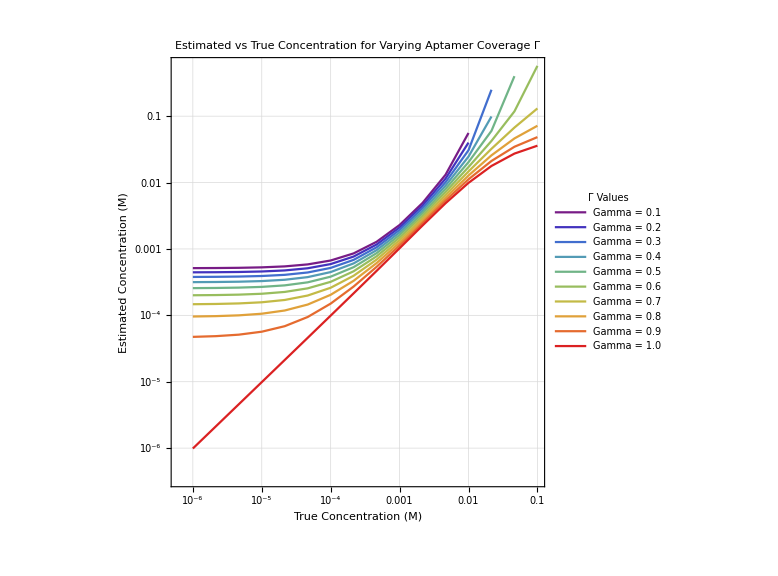

```mathematica
(*------------------------------------------------------------*)(*PREPARE DATA FOR PLOTTING*)(*------------------------------------------------------------*)(*Extract {True Conc,Estimated Conc} pairs for each Gamma*)
plotDataGamma=Table[allResultsGamma[[idx]][[All,{1,3}]],{idx,Length[allResultsGamma]}];

(*Create a color for each Gamma curve*)
colors=ColorData["Rainbow"]/@Rescale[Range[Length[gammaValues]]];

(*Prepare legend labels*)
legendLabels=("Gamma = "<>ToString[NumberForm[#,{2,1}]])&/@gammaValues;

(*------------------------------------------------------------*)
(*PLOT TRUE VS ESTIMATED CONCENTRATIONS*)
(*------------------------------------------------------------*)

finalGammaPlot=ListLogLogPlot[plotDataGamma,PlotStyle->(Directive[#,Thick]&/@colors),Joined->True,Frame->True,FrameLabel->{"True Concentration (M)","Estimated Concentration (M)"},PlotLegends->Placed[LineLegend[colors,legendLabels,LegendLabel->"Γ Values"],Right],GridLines->Automatic,AspectRatio->1,PlotLabel->"Estimated vs True Concentration for Varying Aptamer Coverage Γ",ImageSize->Large,PlotRange->All];

finalGammaPlot
```

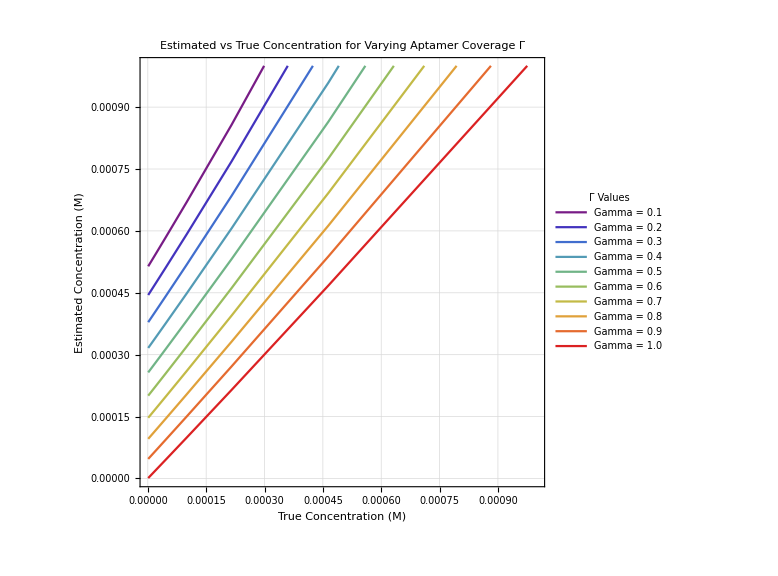

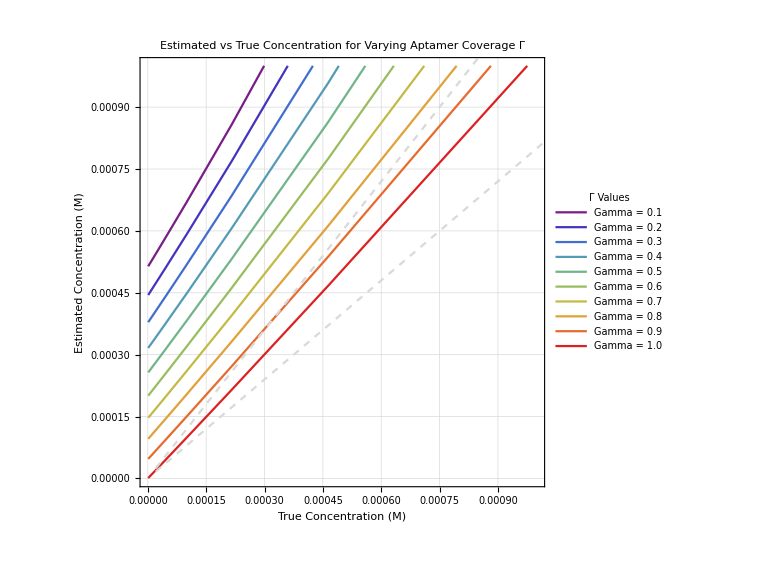

```mathematica
(*------------------------------------------------------------*)(*PREPARE DATA FOR PLOTTING*)(*------------------------------------------------------------*)(*Extract {True Conc,Estimated Conc} pairs for each Gamma*)
plotDataGamma=Table[allResultsGamma[[idx]][[All,{1,3}]],{idx,Length[allResultsGamma]}];

(*Create a color for each Gamma curve*)
colors=ColorData["Rainbow"]/@Rescale[Range[Length[gammaValues]]];

(*Prepare legend labels*)
legendLabels=("Gamma = "<>ToString[NumberForm[#,{2,1}]])&/@gammaValues;

(*------------------------------------------------------------*)
(*PLOT TRUE VS ESTIMATED CONCENTRATIONS*)
(*------------------------------------------------------------*)

finalGammaPlot=ListPlot[plotDataGamma,PlotStyle->(Directive[#,Thick]&/@colors),Joined->True,Frame->True,FrameLabel->{"True Concentration (M)","Estimated Concentration (M)"},PlotLegends->Placed[LineLegend[colors,legendLabels,LegendLabel->"Γ Values"],Right],GridLines->Automatic,AspectRatio->1,PlotLabel->"Estimated vs True Concentration for Varying Aptamer Coverage Γ",ImageSize->Large,PlotRange->{{0,0.001},{0,0.001}}];

finalGammaPlot
Show[finalGammaPlot,errorLines]
```

```mathematica
(* now use forward model given "actual" Conc, Gamma, and Rsol, to generate i25, i200 *)
(* goal: prove that KDM method is good at compensating for gamma to estimate conc, but not Rsol *)

(* generate KDM vs Conc for given typical Gamma and Rsol at representative concentrations *)
(* get representative concentartions list *)

(* get an "effective kD" and a KDM_Max from the KDM vs conc curve at actual measured concentrations at the "in vitro resistance" *)

(* curiosity: how does "effective kD" compare to actual kD? *)
(* answer: kD_effective 3.42 mM vs kD_simulated = 5.26 mM - clearly "kD_effective" is capturing more than just binding kinetics! *)

(* generate KDM vs Gamma for given typical conc (show it's flat) *)


(* use KDM model: Conc,est = Kd,eff * KDM_measured/(KDM_max - KDM_measured) - show Conc_est vs Conc_actual for different values of:
Rsol, Gamma - maybe some small deviations?
*)
KDMestimatedConc = kDfit/. fitResult* KDMMeasured/(kdmMax/. fitResult- KDMMeasured)

(* show that KDM is not robust to solution resistance *)
(* KDM vs conc for different Rsol (already done)  *)
(* estimated conc vs "actual conc" for different Rsol - percent error expected *)


(* intermediate "solutions" - get one value for in vitro Rsol - assume it doesn't change after that *)
(* under those conditions - how much better is a 2-parameter model than KDM? can we just add a correction factor? *)


(* use a 2-frequency fit model to estimate Conc, Gamma (assume Rsol not varying) - is this better than KDM? who cares... *)
(* show percent error in (Cest-Cactual)/Cactual for typical Rsol from 1000 down to 0 and up to 2500 *)
(* show percent error in (Cest-Cactual)/Cactual for typical Gamma from 1 down to 0 *)
(* show percent error in (Cest-Cactual)/Cactual for typical Conc from 0 to 10 mM *)


(* future work: 3 frequency fit *)
```

ReplaceAll::reps: {-KDMMeasured+(kDfit→0.00347339),-KDMMeasured+(kdmMax→1.63235)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {(KDMMeasured (kDfit→0.00347339))/(kdmMax/.{-KDMMeasured+(kDfit→0.00347339),-KDMMeasured+(kdmMax→1.63235)}),(KDMMeasured (kdmMax→1.63235))/(kdmMax/.{-KDMMeasured+(kDfit→0.00347339),-KDMMeasured+(kdmMax→1.63235)})} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

kDfit/.{(KDMMeasured (kDfit→0.00347339))/(kdmMax/.{-KDMMeasured+(kDfit→0.00347339),-KDMMeasured+(kdmMax→1.63235)}),(KDMMeasured (kdmMax→1.63235))/(kdmMax/.{-KDMMeasured+(kDfit→0.00347339),-KDMMeasured+(kdmMax→1.63235)})}

```mathematica
(* future work: improve the model to account for low frequency discrepancies. distribution of R_ct? something else? *)
```

```mathematica
kDFit
```

0.00526958